Type II & Type III Oscillations

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
Quiet[<<"/Users/eden/Desktop/RESEARCH/CODE/Dynamica/Dynamica.m"]
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

## SYSTEMS

## T3 AS

### F3A

```mathematica
Clear[e,h,f,ds,dz,u,v,o,theta,r,k1]
```

```mathematica
T3AS = DynamicalSystem[{
e*((f*A)/(h^2+A^2))*S*A - ds*S ,
r*A*(1 - A/k1)-((f*A)/(h^2+A^2))*A*S
},
{{S,0,80},{A,-0.01,10}},
{{e,0,1000},{h,0,1},{f,0,1},{ds,0.001,0.14},{r,0,2},{k1,0.01,6}}]
```

DynamicalSystem[«2 ODEs»,{S,A},{e,h,f,ds,r,k1}]

```mathematica
T3AS = T3AS/.{e->8,h -> 0.2314, f->0.0153, ds->0.035, r->1,k1->1}
```

DynamicalSystem[«2 ODEs»,{S,A},{ds→0.035,e→8,f→0.0153,h→0.2314,k1→1,r→1}]

Warning: A convergence failure occurred during continuation

Warning: A convergence failure occurred during continuation

Warning: A convergence failure occurred during continuation

«1 more identical outputs»

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {S,A,k,ds}={0,0,0.01,0}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {S,A,k,ds}={0,0.0210016787582075,0.0210016787571253,0.001}

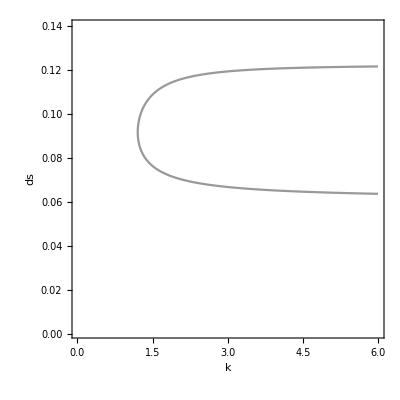

```mathematica
PCT3AS = DisplayParameterChart[T3AS,{k,ds},MaxStepSize->0.1,MaxSteps->10000, Tries->10000]
```

#### Sin

```mathematica
dAT3AS = r*A*(1 - A/k1)-((f*A)/(h^2+A^2))*A*S;
dST3AS= e*((f*A)/(h^2+A^2))*A*S - ds*S ;
```

Get Boundary S & A to plug into Sin

```mathematica
e = 8;
h = 0.2314;
f = 0.0153;
dz = 0.9;
v = 0.05157;
o = 483.8;
theta = 0.8;
r = 1;
```

```mathematica
S0SA= (e*((f*k1)/(h^2+k1^2))*k1)/ds;
```

```mathematica
S0SA/.{ds->0.12075,k1->2}
```

1.00027

#### Construct Chart

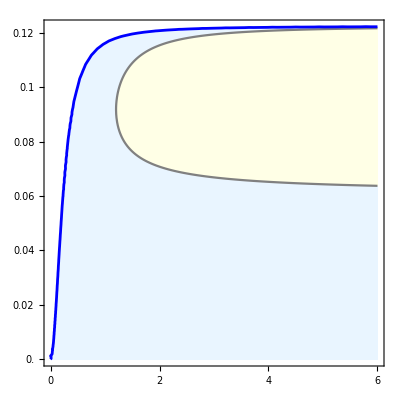

```mathematica
FCT3AS = Show[PCT3AS,
RegionPlot[S0SA>=1 ,{k1,0,6},{ds,0,0.14}, BoundaryStyle->None,PlotStyle->Lighter[LightBlue]],
ListLinePlot[PCT3AS[[1]][[1]][[1]][[3]][[1]],PlotStyle->Gray,Filling->Top,FillingStyle->Lighter[Yellow,0.9], PlotRange->All],
ContourPlot[S0SA==1,{k1,0,6},{ds,0,0.14},ContourStyle->{Blue,Thickness->0.005}],
(*FrameLabel->{"Carrying Capacity (K)","Host Death Rate (d_S)"},*)
FrameTicks->{{{0.00,0.02,0.04,0.06,0.08,0.10,0.12},None},{{0,1,2,3,4,5,6},None}},FrameLabel->None,LabelStyle->{Black,16}, PlotRange->All]
```

#### Time Series

```mathematica
e = 8;
h = 0.2314;
f = 0.0153;
dz = 0.9;
u = 1.049;
v = 0.05157;
o = 483.8;
theta = 0.8;
r = 1;
```

```mathematica
Clear[ds,k1]
ds = 0.09;
ParaT3AS=ParametricNDSolveValue[{S'[t]== e*((f*A[t])/(h^2+A[t]^2))*S[t]*A[t] - ds*S[t] ,
A'[t] == r*A[t]*(1 - A[t]/k1)-((f*A[t])/(h^2+A[t]^2))*A[t]*S[t],
S[0]==11.17, A[0]==0.325},{S,A},{t,0,6000},{k1}];
```

```mathematica
Manipulate[
Show[LogPlot[Evaluate[#[t]& /@ParaT3AS[k1]],{t,0,5500},PlotRange->{{100,300},{0.01,100}},
 PlotStyle->{{Blue,Thick},{Darker[Green],Thick}},
PlotLegends->{"Susceptible","Algae"},TicksStyle->10,AspectRatio->1, LabelStyle->16, Frame->True, FrameLabel->{"Time","Log Concentration"}, FrameStyle->Black]],
{{k1,2},1,8}]
```

### F3C

```mathematica
Clear[e,h,f,ds,dz,u,v,o,theta,r,k1]
```

```mathematica
T3AS = DynamicalSystem[{
e*((f*A)/(h^2+A^2))*S*A - ds*S ,
r*A*(1 - A/k1)-((f*A)/(h^2+A^2))*A*S
},
{{S,0,80},{A,-0.01,10}},
{{e,0,1000},{h,0,1},{f,0,1},{ds,0.001,0.14},{r,0,2},{k1,0.01,6}}]
```

DynamicalSystem[«2 ODEs»,{S,A},{e,h,f,ds,r,k1}]

```mathematica
T3AS = T3AS/.{e->8,h -> 0.2314, f->0.0153, ds->0.035, r->1,k1->1}
```

DynamicalSystem[«2 ODEs»,{S,A},{ds→0.035,e→8,f→0.0153,h→0.2314,k1→1,r→1}]

```mathematica
traj = DisplayTrajectories[T3AS/.{k1->3,ds->0.1},{{56.6809,1.4511}},140, StateVariables->{A,S}, MaxSteps->Infinity, PlotRange->{{0,All},{0,All}}, PlotStyle->{Blue,Thickness[0.018]},FrameLabel->None];
```

```mathematica
Last[First[$Trajectories]]
```

{56.5811,1.45982}

```mathematica
dAT3AS = r*A*(1 - A/k1)-((f*A)/(h^2+A^2))*A*S;
dST3AS= e*((f*A)/(h^2+A^2))*A*S - ds*S ;
```

```mathematica
solsT3AS = Solve[{dAT3AS==0 ,dST3AS==0},{A,S}];
```

```mathematica
e = 8;
h = 0.2314;
f = 0.0153;
r = 1;
k1 = 2;
ds = 0.117;
```

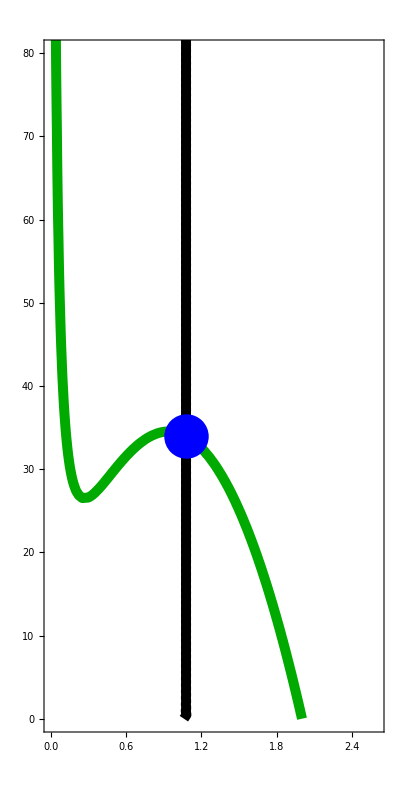

```mathematica
Show[
(*traj,*)
ContourPlot[dAT3AS==0,{A,0,10},{S,0,150}, PlotPoints->100, ContourStyle->{Darker[Green],Thickness[0.018]}],
ContourPlot[dST3AS==0,{A,0,10},{S,0,150}, PlotPoints->100, ContourStyle->{Black,Thickness[0.018]}],
Graphics[{PointSize->0.08,Blue,Point[{solsT3AS[[2]][[1]][[2]],solsT3AS[[2]][[2]][[2]]}]}],
PlotRange->{{0,2.6},{0,80}},AspectRatio->2,LabelStyle->{Black,16}
]
```

```mathematica
dST2AS
```

(0.1224 A S)/(0.2314+A)-ds S

### F3E

```mathematica
Clear[e,h,f,ds,dz,u,v,o,theta,r,k]
```

```mathematica
dAT3AS = r*A*(1 - A/k1)-((f*A)/(h^2+A^2))*A*S;
dST3AS= e*((f*A)/(h^2+A^2))*S*A - ds*S ;
```

```mathematica
solsT3AS = Solve[{dAT3AS==0,dST3AS==0},{A,S},WorkingPrecision->MachinePrecision];
```

```mathematica
solsT3AS[[2]]
```

{A→(√ds h)/(√(-ds+e f)),S→(ds e h^2 r+(ds^(3/2) e h k1 r)/(√(-ds+e f))-(√ds e^2 f h k1 r)/(√(-ds+e f)))/(ds^2 k1-ds e f k1)}

```mathematica
AstarT3AS:=(√ds h)/(√(-ds+e f))
SstarT3AS := (ds e h^2 r+(ds^(3/2) e h k1 r)/(√(-ds+e f))-(√ds e^2 f h k1 r)/(√(-ds+e f)))/(ds^2 k1-ds e f k1)
```

```mathematica
(*Clear[k1];*)
e = 8;
h = 0.2314;
f = 0.0153;
dz = 0.9;
u = 1.049;
v = 0.05157;
o = 483.8;
r = 1;
theta = 0.8;
ds=0.09;
k1 = 2;
```

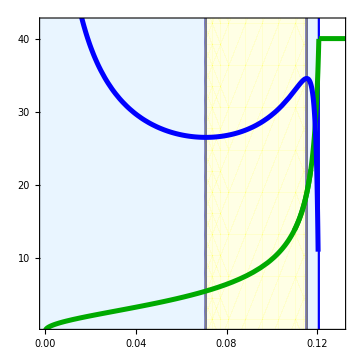

```mathematica
P2 = Show[
RegionPlot[0.07079 > x>-1,{x,-1,0.14},{y,0,100}, BoundaryStyle->{Blue},PlotStyle->{Lighter[LightBlue]}],
RegionPlot[0.12078 > x>0.115396,{x,0,0.14},{y,-10,100}, BoundaryStyle->{Blue},PlotStyle->{Lighter[LightBlue]}],
RegionPlot[0.115396 > x>0.07079,{x,0,0.14},{y,-10,100}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],
Plot[k1*20,{ds,0.12078,0.15}, PlotStyle->{Darker[Green], Thickness[0.01]}],
Plot[AstarT3AS*20,{ds,0,0.15}, PlotStyle->{Darker[Green],Thickness[0.01]}],
Plot[AstarT3AS*20,{ds,0.11,0.12078}, PlotStyle->{Darker[Green],Thickness[0.01]}],
Plot[SstarT3AS,{ds,0,0.16}, PlotStyle->{Blue,Thickness[0.01]}],

PlotRange->{{0,0.13},{1,42}},
FrameTicks->{{{0,10,20,30,40},None},{{{0.00,"0.00"},0.02,0.04,0.06,0.08,{0.10,"0.10"},0.12,0.14},None}},
Frame->True, AspectRatio->1,LabelStyle->{Black,16},ImageSize->Medium
]
```

### F3G

```mathematica
Clear[e,h,f,ds,dz,u,v,o,theta,r,k1]
```

```mathematica
J11T3AS = FullSimplify[D[dAT3AS/A,A]]
```

-r/k1+(f (A-h) (A+h) S)/((A^2+h^2)^2)

```mathematica
Clear[ds]
SelfLim = -r/k1;
Clearance = (f (AstarT3AS-h) (AstarT3AS+h) SstarT3AS)/((AstarT3AS^2+h^2)^2);
```

```mathematica
e = 8;
h = 0.2314;
f = 0.0153;
dz = 0.9;
u = 1.049;
v = 0.05157;
o = 483.8;
r = 1;
theta = 0.8;
k1=2;
```

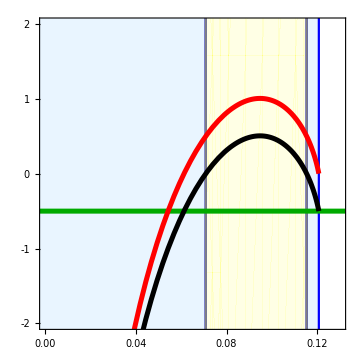

```mathematica
P4 = Show[
RegionPlot[0.07079 > x>-1,{x,-1,0.14},{y,-10,100}, BoundaryStyle->{Blue},PlotStyle->{Lighter[LightBlue]}],
RegionPlot[0.12078 > x>0.115396,{x,0,0.14},{y,-10,100}, BoundaryStyle->{Blue},PlotStyle->{Lighter[LightBlue]}],
RegionPlot[0.115396 > x>0.07079,{x,0,0.14},{y,-10,100}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],
Plot[SelfLim,{ds,-1,0.15}, PlotStyle->{Darker[Green],Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Clearance,{ds,0,0.12078}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[SelfLim + Clearance,{ds,0,0.12078}, PlotStyle->{Black,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

PlotRange->{{0,0.13},{-2,2}},AxesOrigin->{0,0},Axes->True,
FrameTicks->{{{-2,-1,0,1,2},None},{{{0.00,"0.00"},0.02,0.04,0.06,0.08,{0.10,"0.10"},0.12,0.14},None}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium
]
```

## T3 ASI

### F3B / FA6A

```mathematica
Clear[e,h,f,ds,dz,u,v,o,theta,r,k1]
```

```mathematica
T3ASI = DynamicalSystem[{
r*A*(1 - A/k1)-((f*A)/(h^2+A^2))*A*(S+theta*F),
e*((f*A)/(h^2+A^2))*(S+theta*F)*A - ds*S - u*S*F,
u*S*F - (ds + v)*F
},
{{A,-0.01,10},{S,-0.01,200},{F,-0.01,200}},
{{e,0,1000},{h,0,1},{f,0,1},{ds,0.001,0.14},{u,0,2},{v,0,0.2},{theta,0,1},{r,0,2},{k1,0.01,6}}]
```

DynamicalSystem[«3 ODEs»,{A,S,F},{e,h,f,ds,u,v,theta,r,k1}]

```mathematica
T3ASI = T3ASI/.{e->8,h -> 0.2314, f->0.0153, u->0.0075, v->0.05157, theta->0.8, r->1}
```

DynamicalSystem[«3 ODEs»,{A,S,F},{ds,k1},{e→8,f→0.0153,h→0.2314,r→1,theta→0.8,u→0.0075,v→0.05157}]

General::munfl: 0.-7.63773154829383×10^-317 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.-4.22779193008997×10^-316 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.-1.06387290100038×10^-313 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {A,S,F,k1,ds}={0,0,0,6,0}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {A,S,F,k1,ds}={0.01,0,0,0.01,0.000228162568066635}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {A,S,F,k1,ds}={0.0210016787592897,0,0,0.0210016787592897,0.001}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {A,S,F,k1,ds}={0.0210016787592897,7.00933333333333,0,0.021915989450528,0.001}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {A,S,F,k1,ds}={5.62235338982394,23.1684021308521,0,6,0.122193015981391}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {A,S,F,k1,ds}={6.,0,0,6,0.122218214122094}

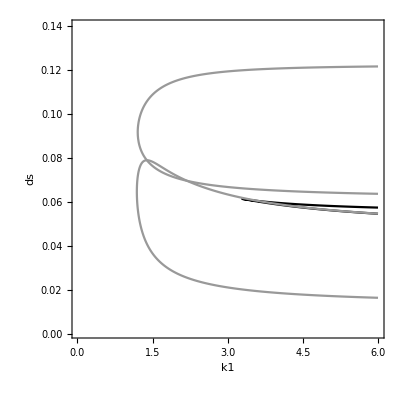

```mathematica
PCT3ASI = DisplayParameterChart[T3ASI,{k1,ds},MaxSteps->Infinity, MaxStepSize->0.1]
```

#### R0 & Sin

```mathematica
Clear[e,h,f,ds,u,v,theta,r,k1]
```

```mathematica
dAT3ASI=r*A*(1 - A/k1)-((f*A)/(h^2+A^2))*A*(S+theta*F);
dST3ASI=e*((f*A)/(h^2+A^2))*A*(S+theta*F) - ds*S - u*S*F;
dFT3ASI=u*S*F - (ds + v)*F;
```

```mathematica
solsT3ASI=Solve[{dST3ASI==0,dFT3ASI==0,dAT3ASI==0},{S,F,A}];
```

```mathematica
solsT3ASI[[4]]/.{ds->0.035,k1->1}
```

{S→28.5714 ((0.187083 e h r)/(√(-0.035+e f))-(0.035 e h^2 r)/(-0.035+e f)),F→0,A→(0.187083 h)/(√(-0.035+e f))}

```mathematica
solsT3ASI[[4]]
```

{S→(-(ds e h^2 r)/(-ds+e f)+(√ds e h k1 r)/(√(-ds+e f)))/(ds k1),F→0,A→(√ds h)/(√(-ds+e f))}

Get Boundary S & A to plug into R0

```mathematica
SatBT3ASI=solsT3ASI[[4,1,2]];
AatBT3ASI=solsT3ASI[[4,3,2]];
```

R0 Equation

```mathematica
R0T3ASI= (u*SatBT3ASI)/(ds+v);
```

```mathematica
S0T3ASI = (e*((f*k1)/(h^2+k1^2))*k1)/ds;
```

#### R0 on cycles - R0 average (FA2B)

```mathematica
Clear[k1,k,d,ds, r0, r0current,stest,a];
```

```mathematica
R0CYC[k0_,ds0_]:=
Module[{k=k0, d = ds0},
(* Equilibrate *)
DisplayTrajectories[T3ASI/.{k1->k,ds->d},{{2,15,0}},500, StateVariables->{A,S}, MaxIterations->Infinity,MaxSteps->Infinity];
(* R0 *)
DisplayTrajectories[T3ASI/.{k1->k,ds->d},{{Last[First[$Trajectories]][[1]],Last[First[$Trajectories]][[2]],0}},2500, StateVariables->{A,S}, MaxIterations->Infinity,MaxSteps->Infinity,MaxStepSize->0.001];
r0 = 0;
For[a=1,a<=Length[$Trajectories[[1]]],a++,
stest = $Trajectories[[1]][[a]][[2]];
r0current = (u*stest)/(d+v);
r0 = r0 + r0current;
];
r0 = r0/Length[$Trajectories[[1]]];
r0
]
```

```mathematica
granK = 0.025; (* 0.025 *)
granDS = 0.001; (* 0.0005 *)
startK = 1;
startDS = 0.06;
maxK = 6;
maxDS = 0.122; (* 0.115 *)
```

```mathematica
e = 8;
h = 0.2314;
f = 0.0153;
u = 0.0075;
v = 0.05157;
theta = 0.8;
r = 1;
```

```mathematica
R0cycdataT3 = {};
For[i=(startK/granK),i<=(maxK/granK),i++,
Clear[k];
k = i * granK;
For[j=(startDS/granDS),j<=(maxDS/granDS),j++,
Clear[d];
d = j * granDS;
AppendTo[R0cycdataT3,{k, d,R0CYC[k,d]}];
]
]
```

```mathematica
Export["R0cycleT3.dat",R0cycdataT3];
```

```mathematica
R0cycdataT3=Import["R0cycleT3.dat","Data"];
```

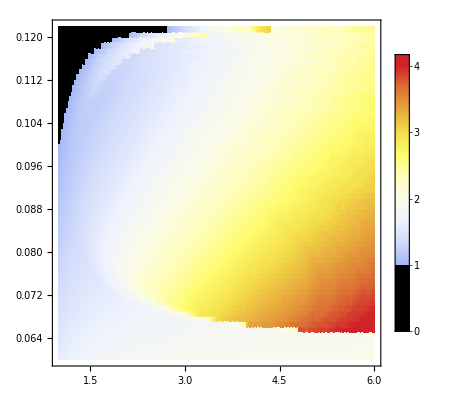

```mathematica
R0cycplot =ListDensityPlot[Transpose[ArrayReshape[R0cycdataT3[[All,3]]/.{u -> 0.0075,
v -> 0.05157},{IntegerPart[(maxK/granK) - (startK/granK)+1],IntegerPart[(maxDS/granDS)-(startDS/granDS)+1]}]],DataRange->{{startK,maxK},{startDS,maxDS}},ColorFunction->(If[#<1,Black,ColorData["TemperatureMap",#/4]]&),ColorFunctionScaling->False,
InterpolationOrder->0, PlotLegends->Automatic]
```

```mathematica
R0PT3ASI= Show[
R0cycplot ,

RegionPlot[R0T3ASI>=1 ,{k1,0,6.5},{ds,0.055,0.14}, BoundaryStyle->{Red,Thickness->0.01},PlotStyle->Opacity[0.0], PlotPoints->200],

ContourPlot[Re[S0T3ASI]==1,{k1,startK,maxK},{ds,0.05,0.14},ContourStyle->{Blue,Thickness->0.01}],
ContourPlot[Re[R0T3ASI]==1,{k1,startK,maxK},{ds,0.05,0.14},ContourStyle->{Red,Thickness->0.01}],

ListLinePlot[LPC1, PlotStyle->{Darker[Blue],Dashed,Thickness->0.008},Filling->Top],

ListLinePlot[PCT3ASI[[1]][[1]][[3]][[3]][[1]],PlotStyle->{Gray, Thickness->0.008},PlotRange->All],

ListLinePlot[PCT3ASI[[1]][[1]][[2]][[3]][[1]],PlotStyle->{Gray, Thickness->0.008,Dashed},PlotRange->All],

ListLinePlot[PCT3ASI[[1]][[1]][[1]][[2]][[1]],PlotStyle->{Black,Thickness->0.007},PlotRange->All],
ListLinePlot[HomoClinic,PlotStyle->{Orange,Dashed,Thickness->0.007},PlotRange->All],

ImageSize->Medium,
FrameTicks->{{{{0.00,"0.00"},0.02,0.04,0.06,0.08,{0.10,"0.10"}, 0.12},None},{{0,1,2,3,4,5,6},None}},
(*FrameLabel->{"Carrying Capacity (K)","Host Death Rate (d_S)"},*)
LabelStyle->{16,Black},AxesOrigin->{0,0},
AspectRatio->1,PlotRange->{{startK,maxK},{startDS,maxDS}}, PlotRangeClipping->True,ImageResolution->1000
]
```

GreaterEqual::nord: Invalid comparison with 0.146597-1.46005 ⅈ attempted.

GreaterEqual::nord: Invalid comparison with 12.7992-13.1093 ⅈ attempted.

GreaterEqual::nord: Invalid comparison with 44.1156-24.3741 ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

-Graphics-

#### Construct Chart

```mathematica
Clear[k1,ds]
e = 8;
h = 0.2314;
f = 0.0153;
u = 0.0075;
v = 0.05157;
theta = 0.8;
r = 1;
```

```mathematica
(* Found manually, use DisplayTrajectories *)
LPC1 = {{1.4,0.04152},{1.5,0.03752},{1.6,0.03452},{1.7,0.03202},{1.8,0.03002},{1.9,0.02722},{2.0,0.02722},
{2.1,0.02612},{2.2,0.02515},{2.3,0.02432},{2.4,0.02352},{2.5,0.02282},{2.6,0.02218},{2.7,0.02161},{2.8,0.02108},
{2.9,0.02060},{3.0,0.02016},{3.1,0.01977},{3.2,0.0194},{3.3,0.01907},{3.4,0.01875},{3.5,0.01847},{3.6,0.01820},
{3.7,0.01796},{3.8,0.01773},{3.9,0.01752},{4.0,0.01732},{4.1,0.01714},{4.2,0.01697},{4.3,0.01681},{4.4,0.01665},
{4.5,0.01651},{4.6,0.01637},{4.7,0.01624},{4.8,0.01612},{4.9,0.01601},{5.0,0.0159},{5.1,0.01579},{5.2,0.01569},
{5.3,0.01559},{5.4,0.0155},{5.5,0.01542},{5.6,0.01533},{5.7,0.01525},{5.8,0.01517},{5.9,0.01509},{6.0,0.01503}};
```

```mathematica
(* Approximated from lower branch of fold bifurcation *)
HomoClinic = {{3.28805391821168873146682769314895838172`15.954589770191003,0.06146585333413837773723345606742076017`15.954589770191003},{3.28806655117714534711541327112936705126`15.954589770191003,0.06146580484770995887990097212507935764`15.954589770191003},{3.28829833033877821932060716036900527262`15.954589770191003,0.06146491681005628494100368101381193615`15.954589770191003},{3.28873140528816110876713276587807394654`15.954589770191003,0.06146325227237109964309930060999023469`15.954589770191003},{3.28935003864379842702372629175073051599`15.954589770191003,0.06146086734902749750776385419596138316`15.954589770191003},{3.29014028094023971519896409578792421426`15.954589770191003,0.06145781224290944567989277556038433342`15.954589770191003},{3.29108970637066771279269485216589959109`15.954589770191003,0.06145413208340525099917153563827205996`15.954589770191003},{3.29218719610367392430269808981950952105`15.954589770191003,0.06144986761728941369659420430593934448`15.954589770191003},{3.29342275917645831443193984392111813096`15.954589770191003,0.06144505578288975891783962727843033819`15.954589770191003},{3.29478738334830449917438852891981258819`15.954589770191003,0.06143973019078659445245168265300133018`15.954589770191003},{3.29627291005087936889899354278898109972`15.954589770191003,0.06143392152900664230899436838393931592`15.954589770191003},{3.2978719288754784260490642551965164873`15.954589770191003,0.06142765790673236674973590662315081152`15.954589770191003},{3.29957768801884810168218528337776560607`15.954589770191003,0.06142096514757175551740269413011618991`15.954589770191003},{3.30138401785575757195765732273612071612`15.954589770191003,0.06141386704115932415148600202095293393`15.954589770191003},{3.30328526537865500213931298562174951111`15.954589770191003,0.06140638556011452814147753380987594842`15.954589770191003},{3.30527623768893471438156590080529256088`15.954589770191003,0.0613985410480212911305131517802100081`15.954589770191003},{3.30735215306999191125171642426004107052`15.954589770191003,0.06139035238303191217021860539938393652`15.954589770191003},{3.30950859844522693195469005245430867395`15.954589770191003,0.06138183712085607999756001114909111324`15.954589770191003},{3.31174149224002299043735693399264469975`15.954589770191003,0.06137301162022939403881901758148572615`15.954589770191003},{3.31404705183869498808485636897148824656`15.954589770191003,0.06136389115342191093762879092407718636`15.954589770191003},{3.31642176496697887322867672294679185761`15.954589770191003,0.06135449000391199755221136429611794775`15.954589770191003},{3.31886236444104135063435751957270725219`15.954589770191003,0.06134482155300911919108103342110484656`15.954589770191003},{3.32136580581607854186762507270497967902`15.954589770191003,0.06133489835691746157166634961066244247`15.954589770191003},{3.32392924754181325525069766762167647301`15.954589770191003,0.0613247322155017919276288803410545739`15.954589770191003},{3.32655003329226636387171744892259875759`15.954589770191003,0.06131433423382648253825921948123490479`15.954589770191003},{3.32922567618918167774621209125019102621`15.954589770191003,0.06130371487737528042006820574728724497`15.954589770191003},{3.33195384467871169139199209998489003897`15.954589770191003,0.06129288402173037664355090172229247954`15.954589770191003},{3.33473234985713284376650613194887075546`15.954589770191003,0.06128185099737686143326947459659104543`15.954589770191003},{3.33755913406932062398419215751640326594`15.954589770191003,0.06127062463020711231515448123099456756`15.954589770191003},{3.34043226062930583171567902825727351018`15.954589770191003,0.06125921327821940563122501863534469785`15.954589770191003},{3.34334990453200428324970358552577161292`15.954589770191003,0.06124762486484088322737623288047330243`15.954589770191003},{3.34631034404316646545467503285912237449`15.954589770191003,0.06123586690924781811037973723540978826`15.954589770191003},{3.34931195306918727866476804917372634535`15.954589770191003,0.06122394655400866589870945008820522128`15.954589770191003},{3.35235319422130940964808458199298558369`15.954589770191003,0.06121187059033358829057869835819192691`15.954589770191003},{3.35543261249930545634071641184073584525`15.954589770191003,0.06119964548118048377124182017475641804`15.954589770191003},{3.35854882952916213256569358728162265479`15.954589770191003,0.06118727738243623783092479478735543412`15.954589770191003},{3.36170053829721904399661361948190367555`15.954589770191003,0.06117477216236644766313891971032873357`15.954589770191003},{3.36488649832999520086393889187368779452`15.954589770191003,0.0611621354195043282056978737281372227`15.954589770191003},{3.36810553127533026468349713621799416523`15.954589770191003,0.06114937249912876723506096166327324585`15.954589770191003},{3.37135651684474981984814365384211271595`15.954589770191003,0.06113648850846752131397919318696097226`15.954589770191003},{3.37463838908266407336439798860787278676`15.954589770191003,0.06112348833074243202497420201119663668`15.954589770191003},{3.37795013293050136176562826435902845801`15.954589770191003,0.06111037663816518045457623086983423276`15.954589770191003},{3.38129078105896242325653703479361491245`15.954589770191003,0.06109715790397602016843369461926334901`15.954589770191003},{3.38465941094274556716178793645343136031`15.954589770191003,0.06108383641361275797143396602416862014`15.954589770191003},{3.38805514215643685773396937209457591925`15.954589770191003,0.06107041627508411473910508041174583775`15.954589770191003},{3.39147713387126854843773465082464189035`15.954589770191003,0.06105690142861732768285187132385004127`15.954589770191003},{3.39492458253536587212564031294887378042`15.954589770191003,0.06104329565564006488328373717901111081`15.954589770191003},{3.39839671972136128578034582105264481511`15.954589770191003,0.06102960258715298371250783016398152007`15.954589770191003},{3.40189281012698999117700341259100350202`15.954589770191003,0.06101582571154349782354315339629147895`15.954589770191003},{3.40541214971612319968783484394727448149`15.954589770191003,0.06100196838188370990927681110096184729`15.954589770191003},{3.40895406398802860584301857152372045828`15.954589770191003,0.06098803382275658479453913907364815344`15.954589770191003},{3.41251790636478985409828452364861687879`15.954589770191003,0.06097402513664491950990579309828170267`15.954589770191003},{3.41610305668721452880832512076457647366`15.954589770191003,0.06095994530991766512279436240768890831`15.954589770191003},{3.41970891981028726503916328006748491476`15.954589770191003,0.06094579721844568487293802237763064798`15.954589770191003},{3.42333492429089236426985999124389917117`15.954589770191003,0.06093158363287220454593599141896679487`15.954589770191003},{3.42698052116001026703745095233883881817`15.954589770191003,0.06091730722356617641586194838856039807`15.954589770191003},{3.43064518277347950626311275710236983169`15.954589770191003,0.06090297056527958436223943046670950147`15.954589770191003},{3.43432840173496885612506945442326627453`15.954589770191003,0.06088857614153184257732861745805231269`15.954589770191003},{3.43802968988595765577925294524999751238`15.954589770191003,0.06087412634873927876946348970559467386`15.954589770191003},{3.44174857735779888138250579063323446564`15.954589770191003,0.06085962350010868495289457206569589325`15.954589770191003},{3.44548461168115053562415548119013213126`15.954589770191003,0.06084506982931085639126849392370304438`15.954589770191003},{3.44923735694900378771534533836672591469`15.954589770191003,0.06083046749394870199593096938066078796`15.954589770191003},{3.45300639302898108469355006822759034148`15.954589770191003,0.06081581857883516807605796755556637348`15.954589770191003},{3.45679131482205135921379033560459826359`15.954589770191003,0.06080112509909184392327364331008850698`15.954589770191003},{3.46059173156384507339320376666348287589`15.954589770191003,0.06078638900308202109973461738232516909`15.954589770191003},{3.46440726616611792349178883183859120124`15.954589770191003,0.06077161217518734230023796390010940457`15.954589770191003},{3.46823755459534573628016077015539369715`15.954589770191003,0.06075679643843917162701218852677617601`15.954589770191003},{3.47208224528608330134979766707177557055`15.954589770191003,0.06074194355701349132328604046953557825`15.954589770191003},{3.47594099858678930835300488522111444818`15.954589770191003,0.06072705523859795221785154776831731425`15.954589770191003},{3.47981348623587496482003301085033639498`15.954589770191003,0.06071213313663893452579508796960025441`15.954589770191003},{3.4836993908662522887604727364493276505`15.954589770191003,0.06069717885247628323467140938783862879`15.954589770191003},{3.48759840553610981710916494356800150092`15.954589770191003,0.06068219393737262246438589432073239087`15.954589770191003},{3.49151023328491111014989232950193387607`15.954589770191003,0.0606671798944426266188199468648758532`15.954589770191003},{3.49543458671234822495324138882539974643`15.954589770191003,0.0606521381804894809717918372585078676`15.954589770191003},{3.49937118757929909826628259746320363355`15.954589770191003,0.06063707020775323747203430880965643699`15.954589770191003},{3.50331976642919597091508984289831468292`15.954589770191003,0.06062197734557615349958068655757960014`15.954589770191003},{3.50728006222865667483104658123330509679`15.954589770191003,0.06060686092199041714480575265106234946`15.954589770191003},{3.51125182202618937780395865396072961903`15.954589770191003,0.0605917222252317034946838463032904276`15.954589770191003},{3.5152348006279363564766774590459272825`15.954589770191003,0.06057656250518360074212015628961044168`15.954589770191003},{3.51922876028932570951318881573896631604`15.954589770191003,0.06056138297475643332040797944230201228`15.954589770191003},{3.52323347042189194332572884618638664491`15.954589770191003,0.06054618481120368428624414359078505638`15.954589770191003},{3.52724870731416559232588869383989067733`15.954589770191003,0.06053096915738045316271802834675236533`15.954589770191003},{3.53127425386603148776004989001889351988`15.954589770191003,0.06051573712294601974140662772725063693`15.954589770191003},{3.53530989933571643912225197425514666085`15.954589770191003,0.06050048978551381190504317699246359346`15.954589770191003},{3.53935543909851071116483158811233651317`15.954589770191003,0.06048522819175215622040733946453061481`15.954589770191003},{3.54341067441691431916687063097182065368`15.954589770191003,0.06046995335843764661195895618858203725`15.954589770191003},{3.54747541222137320937356241022275480979`15.954589770191003,0.06045466627346359425846374099702082969`15.954589770191003},{3.55154946490089953593032301539694770371`15.954589770191003,0.06043936789680669747597634280694263006`15.954589770191003},{3.55563265010340176889294006549857093056`15.954589770191003,0.06042405916145309583160037840508688858`15.954589770191003},{3.55972479054480510171812708357106672257`15.954589770191003,0.06040874097428638675532484497677934249`15.954589770191003},{3.56382571382681206538343606706672699471`15.954589770191003,0.06039341421693921032289387660404114442`15.954589770191003},{3.56793525226261251305402274826652463681`15.954589770191003,0.06037807974661089841158034703479317315`15.954589770191003},{3.57205324271032473148024694075072752492`15.954589770191003,0.06036273839685130194144927926421042257`15.954589770191003},{3.57617952641354688398733700491012207083`15.954589770191003,0.06034739097831490797974672009732379462`15.954589770191003},{3.58031394884890105174505676709836482658`15.954589770191003,0.06033203827948375794730700608367165032`15.954589770191003},{3.58445635957998248998384362081691400053`15.954589770191003,0.06031668106736320638429885605203113436`15.954589770191003},{3.58860661211760011486757633471709156978`15.954589770191003,0.06030132008815013385067070145117530966`15.954589770191003},{3.59276456378574364718203619411721436696`15.954589770191003,0.06028595606787574594782236282918157798`15.954589770191003},{3.59693007559325283111683225515622723436`15.954589770191003,0.06027058971302422548771998171900666551`15.954589770191003},{3.60110301211077484354366982833248302439`15.954589770191003,0.06025522171112685616367025837734319061`15.954589770191003},{3.60528324135270342816267215051176087291`15.954589770191003,0.06023985273133560019650016146574198338`15.954589770191003},{3.60947063466395964151965826846897706126`15.954589770191003,0.06022448342497393118309049460014431474`15.954589770191003},{3.61366506661134832974465983754742239898`15.954589770191003,0.06020911442606805545693116451295921235`15.954589770191003},{3.61786641487922085729669558415842837753`15.954589770191003,0.06019374635185881395391229067865386335`15.954589770191003},{3.62207456016936851751716555302526467349`15.954589770191003,0.06017837980329446118159577291982186991`15.954589770191003},{3.62628938610475522218376512798887814918`15.954589770191003,0.06016301536550634040303094242765444194`15.954589770191003},{3.63051077913704806853196910907567966919`15.954589770191003,0.06014765360826733347117320736402851963`15.954589770191003},{3.63473862845784222966571321496310866382`15.954589770191003,0.06013229508643383354461709028965170262`15.954589770191003},{3.63897282591310907163694937464426778547`15.954589770191003,0.06011694034037279026716104550273259779`15.954589770191003},{3.64321326592109365007114847763254756041`15.954589770191003,0.06010158989637320371449990267512698391`15.954589770191003},{3.64745984539326533431167225545974420317`15.954589770191003,0.06008624426704364216840670448197659192`15.954589770191003},{3.65171246365817504196482745884134958945`15.954589770191003,0.06007090395169660869496359169094034045`15.954589770191003},{3.65597102238835793687888572209918636551`15.954589770191003,0.06005556943671863901499366937874969493`15.954589770191003},{3.66023542552966114022048046871522224167`15.954589770191003,0.06004024119592921585679219684433424318`15.954589770191003},{3.66450557923345526774914404271163163127`15.954589770191003,0.06002491969092656748261913706468923783`15.954589770191003},{3.66878139179116887136749855361047727333`15.954589770191003,0.0600096053714226111113935352303357654`15.954589770191003},{3.67306277357127315474631903119105140312`15.954589770191003,0.05999429867556630257958899826343059682`15.954589770191003},{3.67734963695846607164307274106014576047`15.954589770191003,0.05997900003025668406709505526273955597`15.954589770191003},{3.68164189629514984870698462823745625566`15.954589770191003,0.05996370985144577987360604413078768644`15.954589770191003},{3.68593946782489874077949067904334817969`15.954589770191003,0.05994842854443104989051575733440545574`15.954589770191003},{3.69024226963791033047769428196082457274`15.954589770191003,0.05993315650413951183644708842107416105`15.954589770191003},{3.69455022161853557970474837815898144774`15.954589770191003,0.05991789411540154562808369919308094264`15.954589770191003},{3.69886324539439287177414031358597482637`15.954589770191003,0.0599026417532169136504628930189226252`15.954589770191003},{3.7031812642875010409692363602184740513`15.954589770191003,0.05988739978301185565441766992910967471`15.954589770191003},{3.70750420326684550285839059087058414652`15.954589770191003,0.05987216856088870563052077455355231417`15.954589770191003},{3.71183198890281658397769742969924177817`15.954589770191003,0.05985694843386679675911716905648162523`15.954589770191003},{3.71616454932298698847492106042484322964`15.954589770191003,0.05984173974011688130263798744395215546`15.954589770191003},{3.72050181416948468427920785572544685131`15.954589770191003,0.05982654280918794785358039629616392183`15.954589770191003},{3.72484371455782022353198936914958448521`15.954589770191003,0.05981135796222661328489325223527750655`15.954589770191003},{3.72919018303700158720765658459543697948`15.954589770191003,0.05979618551219100192532974778367867451`15.954589770191003},{3.73354115355100491770264314647638608875`15.954589770191003,0.05978102576405698591067942909194998212`15.954589770191003},{3.7378965614015826805537972404392330118`15.954589770191003,0.05976587901501903030044809524332155501`15.954589770191003},{3.74225634321217558735849430599424768779`15.954589770191003,0.05975074555468455966054527060225221814`15.954589770191003},{3.74662043689303740632422580149453416214`15.954589770191003,0.05973562566526311488275903925090768518`15.954589770191003},{3.75098878160756163894656554485183407361`15.954589770191003,0.0597205196217492837180441030651573621`15.954589770191003},{3.75536131773957635109682186281386990141`15.954589770191003,0.05970542769210083952763511247499842176`15.954589770191003},{3.75973798686174381492960691458594618177`15.954589770191003,0.0596903501374113321807759488004829649`15.954589770191003},{3.76411873170495360933377306016915919115`15.954589770191003,0.05967528721207804713673366546094083158`15.954589770191003},{3.76850349612868422744474624292715827345`15.954589770191003,0.05966023916396455931723923354160645978`15.954589770191003},{3.77289222509226100754882970568858578084`15.954589770191003,0.05964520623455932059719778479662802467`15.954589770191003},{3.77728486462706343832386956297565761179`15.954589770191003,0.05963018865912950470670969266152340221`15.954589770191003},{3.78168136180959521235894311567347333875`15.954589770191003,0.0596151866668698240086932454920919871`15.954589770191003},{3.78608166473524303750849021346948389962`15.954589770191003,0.05960020048104865889643700036289477271`15.954589770191003},{3.79048572249308839588227644736290658614`15.954589770191003,0.05958523031914833862989865796794863611`15.954589770191003},{3.79489348514123094234073247629020161543`15.954589770191003,0.05957027639300314658170598468734454048`15.954589770191003},{3.79930490368305481806382311833481670251`15.954589770191003,0.05955533890893218729659806323947386346`15.954589770191003},{3.80371993004407008551139011710028974741`15.954589770191003,0.05954041806786960838250169454344842354`15.954589770191003},{3.80813851704955203138325065086605708411`15.954589770191003,0.05952551406549053637788058298581981683`15.954589770191003},{3.81256061840276606364349772915388353741`15.954589770191003,0.05951062709233402137999662912029863814`15.954589770191003},{3.81698618866387624549224136877457242276`15.954589770191003,0.05949575733392258319334264786083699502`15.954589770191003},{3.82141518322947859529866659591378533569`15.954589770191003,0.05948090497087838081388398187938918078`15.954589770191003},{3.82584755831270616763457180755161703222`15.954589770191003,0.05946607017903643924321570588599604699`15.954589770191003},{3.83028327092392877578760150687685325978`15.954589770191003,0.05945125312955486881533121228915406427`15.954589770191003},{3.83472227885200285323964588971935610208`15.954589770191003,0.05943645398902193871570424767796881237`15.954589770191003},{3.83916454064611675610690281477313515867`15.954589770191003,0.05942167291956062436475843102259026221`15.954589770191003},{3.84361001559803161282049354721567218723`15.954589770191003,0.05940691007893019255896842350961183761`15.954589770191003},{3.84805866372498110020056403479146294877`15.954589770191003,0.0593921656206252647816127561533432694`15.954589770191003},{3.85251044575287405030206352041890807082`15.954589770191003,0.05937743969397248418879400337371615199`15.954589770191003},{3.8569653231001945804892046423577256949`15.954589770191003,0.05936273244422401533793123952762314874`15.954589770191003},{3.86142325786213365638575463561298437784`15.954589770191003,0.05934804401264955060503699098463272379`15.954589770191003},{3.86588421279530789072234108208520765519`15.954589770191003,0.05933337453662521822510152383600363653`15.954589770191003},{3.87034815130284305328048808051018565`15.954589770191003,0.05931872414972073990587304477848609622`15.954589770191003},{3.87481503741988551350792217283053153162`15.954589770191003,0.05930409298178398100847907251696247879`15.954589770191003},{3.879284835799489838253506878644398386`15.954589770191003,0.05928948115902368079978144467764513196`15.954589770191003},{3.88375751169892177093352537294898928005`15.954589770191003,0.05927488880408991396119102469142396148`15.954589770191003},{3.88823303096631204671676602475551339875`15.954589770191003,0.05926031603615266776694641014783254032`15.954589770191003},{3.89271136002770499699642250405077728878`15.954589770191003,0.05924576297097818424214611860592008509`15.954589770191003},{3.89719246587435638383431534679506941015`15.954589770191003,0.05923122972100410410510370150163270894`15.954589770191003},{3.90167631605049998471053615752566093156`15.954589770191003,0.05921671639541184842179655552677368592`15.954589770191003},{3.90616287864138450291598623036575120835`15.954589770191003,0.05920222310019781833171253624215781554`15.954589770191003},{3.91065212226159496035720457683155373429`15.954589770191003,0.05918774993824270333858373012768347863`15.954589770191003},{3.91514401604372564621306845527219359138`15.954589770191003,0.05917329700937915436647942881053120219`15.954589770191003},{3.91963852962733764902117758671196799027`15.954589770191003,0.0591588644104576722606474388924831691`15.954589770191003},{3.92413563314818884741264475499893034344`15.954589770191003,0.05914445223541105328747668780311681787`15.954589770191003},{3.92863529722775087978328780876017324088`15.954589770191003,0.05913006057531731345976559777083788211`15.954589770191003},{3.93313749296303257428840645393565551127`15.954589770191003,0.05911568951846095843221154662357158639`15.954589770191003},{3.937642191916614225489375903432475765`15.954589770191003,0.0591013391503928275663714317983729605`15.954589770191003},{3.94214936610694192803049542901453312801`15.954589770191003,0.05908700955398863370197838952850301902`15.954589770191003},{3.94665898799893971863070329322348947955`15.954589770191003,0.05907270080950604887048676371656590143`15.954589770191003},{3.95117103049472167935730138695871538916`15.954589770191003,0.05905841299464051321773283931836319683`15.954589770191003},{3.95568546692469178897426072270389997848`15.954589770191003,0.05904414618457948946063917043560169979`15.954589770191003},{3.96020227103875628782234722123829477775`15.954589770191003,0.05902990045205590997210235916189744238`15.954589770191003},{3.96472141699781414760895105091591681612`15.954589770191003,0.05901567586739980087088456133018846675`15.954589770191003},{3.96924287936546026503604518817159425532`15.954589770191003,0.0590014724985893021465369826081292686`15.954589770191003},{3.97376663309978860221987832078955318048`15.954589770191003,0.05898729041130005534831989681135194248`15.954589770191003},{3.97829265354557725791332308921664919822`15.954589770191003,0.05897312966895384708995157899810160339`15.954589770191003},{3.9828209164265395490781473421583552473`15.954589770191003,0.05895899033276560189654460505499692855`15.954589770191003},{3.98735139783778024134851956248582401686`15.954589770191003,0.05894487246178994079761125289960431198`15.954589770191003},{3.99188407423846328656289734836997476176`15.954589770191003,0.05893077611296626861302135654169159507`15.954589770191003},{3.99641892244464330030482512950272919533`15.954589770191003,0.05891670134116279433939746245128357007`15.954589770191003},{4.00095591962225104330741908677822483156`15.954589770191003,0.05890264819922009855566271684606360444`15.954589770191003},{4.00549504328031841249424709504034713065`15.954589770191003,0.05888861673799289281991957924074876668`15.954589770191003},{4.01003627126423771680238415034049154884`15.954589770191003,0.05887460700639167662466884697525412265`15.954589770191003},{4.01457958174929889982145363628106391214`15.954589770191003,0.05886061905142279285372914456790298757`15.954589770191003},{4.01912495323437148546290396664754689073`15.954589770191003,0.05884665291822806240150580394517297263`15.954589770191003},{4.02367236453562757614984549761627021911`15.954589770191003,0.05883270865012333602150951103834966676`15.954589770191003},{4.02822179478054825611330268595360926311`15.954589770191003,0.05881878628863614963021635824162261653`15.954589770191003},{4.0327732234019247725565488404250491814`15.954589770191003,0.0588048858735427319025500449067502324`15.954589770191003},{4.03732663013218335286710441408415636692`15.954589770191003,0.05879100744290409900381863048933912702`15.954589770191003},{4.04188199499768413049900792749209781015`15.954589770191003,0.0587771510331012389193122532360863647`15.954589770191003},{4.04643929831320560748579456347837053486`15.954589770191003,0.05876331667886974210324726989308554872`15.954589770191003},{4.05099852067655673608214028850219302717`15.954589770191003,0.05874950441333363335142007516006184959`15.954589770191003},{4.05555964296334138707564441991174756051`15.954589770191003,0.05873571426803839551183453456800271864`15.954589770191003},{4.06012264632176686870868185977213493661`15.954589770191003,0.05872194627298325452611097334964943373`15.954589770191003},{4.06468751216765583778766494351526706824`15.954589770191003,0.05870820045665297297672827949907950914`15.954589770191003},{4.06925422217950836051580530558704601137`15.954589770191003,0.05869447684604873022204749071614188091`15.954589770191003},{4.07382275829368512324381668439969298486`15.954589770191003,0.05868077546671848918662045758590278722`15.954589770191003},{4.07839310269977132552719350145505886337`15.954589770191003,0.05866709634278667765743960754161890156`15.954589770191003},{4.08296523783591091799601483290784563807`15.954589770191003,0.0586534394969831863497726704123685006`15.954589770191003},{4.08753914638432946657533516286892177351`15.954589770191003,0.05863980495067192591156301945549145319`15.954589770191003},{4.09211481126699399689909080912216934949`15.954589770191003,0.05862619272387852386642158610248029393`15.954589770191003},{4.09669221564126092678042277026199297106`15.954589770191003,0.05861260283531756987498170502930745882`15.954589770191003},{4.10127134289571856901985994190117118188`15.954589770191003,0.05859903530241945963138402555201915727`15.954589770191003},{4.10585217664601347580458005816357538737`15.954589770191003,0.05858549014135646179041027109036155102`15.954589770191003},{4.11043470073091125660392614680050301721`15.954589770191003,0.05857196736706821578189706682271726281`15.954589770191003},{4.11501889920833198287201079263984977598`15.954589770191003,0.05855846699328681589953348461246493166`15.954589770191003},{4.119604756351451340955691477783432115`15.954589770191003,0.05854498903256149467600473584421029771`15.954589770191003},{4.12419225664501809414860599211473786727`15.954589770191003,0.05853153349628238027187814455656697789`15.954589770191003},{4.12878138478161532525138040806170794795`15.954589770191003,0.0585181003947043363638302277086574916`15.954589770191003},{4.13337212565809608049805393259727435357`15.954589770191003,0.05850468973696966712943690818313660009`15.954589770191003},{4.13796446437197287920665730995345039639`15.954589770191003,0.05849130153113121022963403123601924996`15.954589770191003},{4.14255838621807173698558257680231834305`15.954589770191003,0.05847793578417391578093768286799301741`15.954589770191003},{4.14715387668506626825794976890099350881`15.954589770191003,0.05846459250203672638721458053534769314`15.954589770191003},{4.15175092145221429464247396573317144068`15.954589770191003,0.05845127168963401689984556858307778915`15.954589770191003},{4.15634950638606634743152615922915222826`15.954589770191003,0.05843797335087617530022030760014018076`15.954589770191003},{4.16094961753735976949357215699036950112`15.954589770191003,0.05842469748868991520429456346601156562`15.954589770191003},{4.16555124113783443232957241898762101818`15.954589770191003,0.05841144410503854258620896915090233253`15.954589770191003},{4.17015436359725941814434389052932703965`15.954589770191003,0.0583982132009412693668517920904902349`15.954589770191003},{4.17475897150038360145810794320180949756`15.954589770191003,0.05838500477649249951331865640714057688`15.954589770191003},{4.1793650516040750647665172320709869361`15.954589770191003,0.058371818830880646389927316282979318`15.954589770191003},{4.1839725908344215142146415822250191667`15.954589770191003,0.05835865536240653144468151184952072662`15.954589770191003},{4.18858157628392405786875253384808205856`15.954589770191003,0.05834551436850147819841709943932070681`15.954589770191003},{4.19319199520879168584275581275560946836`15.954589770191003,0.05833239584574491258212373150554369865`15.954589770191003},{4.19780383502622391837590142709355732817`15.954589770191003,0.05831929978988176439823399910641763058`15.954589770191003},{4.20241708331172841254577010272878162519`15.954589770191003,0.05830622619583974284213529212055256057`15.954589770191003},{4.20703172779663705299485883979817227935`15.954589770191003,0.05829317505774552342499492122557702045`15.954589770191003},{4.21164775636551342793331311750409304561`15.954589770191003,0.05828014636894139392995823330934009624`15.954589770191003},{4.21626515705362080065987667614449788757`15.954589770191003,0.05826714012200141424782545438102209934`15.954589770191003},{4.22088391804461746061632751136679405381`15.954589770191003,0.05825415630874672862611546215410072989`15.954589770191003},{4.22550402766805797828596653639938344395`15.954589770191003,0.0582411949202614192908590443908716959`15.954589770191003},{4.23012547439711841026100599302074011012`15.954589770191003,0.05822825594690729329850065807223922266`15.954589770191003},{4.23474824684626727338438775495758886727`15.954589770191003,0.05821533937833881209306119341928803128`15.954589770191003},{4.23937233376904275478959300877194713038`15.954589770191003,0.05820244520351771545045961599516847208`15.954589770191003},{4.24399772405583608594573478707416531334`15.954589770191003,0.0581895734107271210511688098794470891`15.954589770191003},{4.24862440673176346488023182568629470017`15.954589770191003,0.05817672398758551607677665834506199026`15.954589770191003},{4.25325237095447491196302978377716264163`15.954589770191003,0.05816389692106073140657564604245462457`15.954589770191003},{4.2578816060121564164272636799814950629`15.954589770191003,0.05815109219748290669276936810519025726`15.954589770191003},{4.26251210132144188699599476992338815891`15.954589770191003,0.05813830980255809837100159688916938203`15.954589770191003},{4.26714384642542893782011405282911923112`15.954589770191003,0.05812554972138114648700157468211374423`15.954589770191003},{4.27177683099171920826497486955236102802`15.954589770191003,0.05811281193844802570650775563639643191`15.954589770191003},{4.27641104481050016681962223304880141211`15.954589770191003,0.05810009643766873231753207140476684602`15.954589770191003},{4.28104647779264949531420210780339909178`15.954589770191003,0.05808740320237934801038301445345412485`15.954589770191003},{4.28568311996786829948098132759982165924`15.954589770191003,0.0580747322153538891606027955618339193`15.954589770191003},{4.29032096148288404374381087578825072751`15.954589770191003,0.05806208345881606560023281752762108891`15.954589770191003},{4.29495999259967854662970360884632611166`15.954589770191003,0.05804945691445111416909987100637971434`15.954589770191003},{4.29960020369371789341545569021056473374`15.954589770191003,0.05803685256341684230201267424786981395`15.954589770191003},{4.30424158525220719104152210999565176835`15.954589770191003,0.05802427038635463803702785046899457565`15.954589770191003},{4.30888412787248455711554530933976244191`15.954589770191003,0.0580117103634006765823244968312057905`15.954589770191003},{4.31352782226030045889234803142737142391`15.954589770191003,0.05799917247419641887675621796481144382`15.954589770191003},{4.31817265922820674866797819656748772097`15.954589770191003,0.05798665669789902108499846779814586618`15.954589770191003},{4.32281862969395645315182107971155393193`15.954589770191003,0.05797416301319188598768269182638160194`15.954589770191003},{4.32746572467899090463388109179937413601`15.954589770191003,0.05796169139829447306607820387255837361`15.954589770191003},{4.33211393530682972890752051039419252048`15.954589770191003,0.05794924183097246641133974759282589582`15.954589770191003},{4.33676325280161354693865644488260045382`15.954589770191003,0.05793681428854732442728035479998482512`15.954589770191003},{4.34141366848658234426507680557303506676`15.954589770191003,0.05792440874790593787523030643838174364`15.954589770191003},{4.34606517378266388162885823275329901823`15.954589770191003,0.05791202518550985223534979611674480363`15.954589770191003},{4.35071776020702825026467110716383027664`15.954589770191003,0.05789966357740465954625801802133779393`15.954589770191003},{4.35537141937165985332992181743916020647`15.954589770191003,0.05788732389922895473580030165757538494`15.954589770191003},{4.36002614298202277452089616846503997729`15.954589770191003,0.05787500612622306025167186853958290188`15.954589770191003},{4.3646819228356759475809413566658912327`15.954589770191003,0.05786271023323797029336097557039649084`15.954589770191003},{4.36933875082095694603430596009141948003`15.954589770191003,0.05785043619474372675867298451760399588`15.954589770191003},{4.37399661891565768277616154261730725298`15.954589770191003,0.0578381839848377547235929397369856658`15.954589770191003},{4.37865551918578026375490185439797544868`15.954589770191003,0.05782595357725331329907213623670587`15.954589770191003},{4.38331544378424174507347281217468740121`15.954589770191003,0.05781374494536723335532167002337496805`15.954589770191003},{4.38797638494966308499566601993399168347`15.954589770191003,0.05780155806220833560881293902244656146`15.954589770191003},{4.39263833500510646809670062053891846796`15.954589770191003,0.05778939290046462012743214885176544898`15.954589770191003},{4.39730128635693453526035391665480898699`15.954589770191003,0.05777724943249143650607147931509092488`15.954589770191003},{4.40196523149360253708111443908070466653`15.954589770191003,0.05776512763031867472532733108349546381`15.954589770191003},{4.40663016298453121408729958779025615783`15.954589770191003,0.05775302746565821632056501284507609694`15.954589770191003},{4.41129607347891528169555826506873142239`15.954589770191003,0.05774094890991131628797984326554021512`15.954589770191003},{4.41596295570469764639223478765331079203`15.954589770191003,0.05772889193417535818833801521863008371`15.954589770191003},{4.4206308024673760644303115118912954536`15.954589770191003,0.05771685650925107956817128151257236681`15.954589770191003},{4.42529960664901252485096566945501387189`15.954589770191003,0.05770484260564960468585391476619585656`15.954589770191003},{4.42996936120710894193756471848220926558`15.954589770191003,0.05769285019359865094208560169075128853`15.954589770191003},{4.43464005917361160611417910351130332535`15.954589770191003,0.05768087924304966225547470407559618361`15.954589770191003},{4.43931169365383683184518658712362478174`15.954589770191003,0.05766892972368392148319296330211396787`15.954589770191003},{4.44398425782553643911699725932542167809`15.954589770191003,0.05765700160491898952025265236748597864`15.954589770191003},{4.44865774493786021612373764557595429528`15.954589770191003,0.05764509485591523451862639736012644819`15.954589770191003},{4.4533321483103584397184786824082391017`15.954589770191003,0.05763320944558164448873132856483887198`15.954589770191003},{4.4580074613321019543734417287544696057`15.954589770191003,0.05762134534258189781904936924975800003`15.954589770191003},{4.4626836774606802799372758570504585367`15.954589770191003,0.05760950251534041796584981042337544675`15.954589770191003},{4.46736079022128526462538393587195827276`15.954589770191003,0.0575976809320481537932796856451860365`15.954589770191003},{4.47203879320583610125137315486464973234`15.954589770191003,0.0575858805606682532614170630349933001`15.954589770191003},{4.4767176800720391201310394685008104844`15.954589770191003,0.05757410136894168529575902630300677878`15.954589770191003},{4.48139744454254300338966854094617134369`15.954589770191003,0.05756234332439275255232527393436480495`15.954589770191003},{4.48607808040405188545938953580503751719`15.954589770191003,0.05755060639433447099335821607044995346`15.954589770191003},{4.49075958150648277528358299138970621979`15.954589770191003,0.05753889054587399099868752460534134625`15.954589770191003},{4.49544194176212972320397202480707405709`15.954589770191003,0.05752719574591764895412277572548965378`15.954589770191003},{4.50012515514484565050310924332194210028`15.954589770191003,0.05751552196117612119639787676931861824`15.954589770191003},{4.50480921568920171717632684331195399683`15.954589770191003,0.05750386915816977286770257231189190204`15.954589770191003},{4.50949411748974963846810034024760759273`15.954589770191003,0.0574922373032330586524445388446163457`15.954589770191003},{4.51417985470015668060046593928253856049`15.954589770191003,0.05748062636251985531490217308782829523`15.954589770191003},{4.51886642153249177895965778686449519087`15.954589770191003,0.05746903630200802252171001296540113173`15.954589770191003},{4.52355381225646501250042691004994544`15.954589770191003,0.05745746708750407934271939908118639202`15.954589770191003},{4.52824202119866499023818310577898577108`15.954589770191003,0.05744591868464785400710437776985983307`15.954589770191003},{4.5329310427418168409524907176626321871`15.954589770191003,0.0574343910589169794639091670677550826`15.954589770191003},{4.53762087132405436698175763218399725633`15.954589770191003,0.05742288417563145012914333941292128476`15.954589770191003},{4.54231150143824415848493021141045348197`15.954589770191003,0.05741139799995778344490475850158187431`15.954589770191003},{4.54700292763124365577606435082086795867`15.954589770191003,0.05739993249691338118155759967491478576`15.954589770191003},{4.55169514450323644728128673472208414484`15.954589770191003,0.05738848763137087464502071470185711372`15.954589770191003},{4.55638814670702878786044738625159068542`15.954589770191003,0.05737706336806209097249476985145725498`15.954589770191003},{4.56108192894740265490082480645964357972`15.954589770191003,0.05736565967158219682912337443144148733`15.954589770191003},{4.56577648598046425780295709019098433299`15.954589770191003,0.05735427650639370498646589936455756062`15.954589770191003},{4.57047181261295844158678233195901291322`15.954589770191003,0.05734291383683021510445049755481262741`15.954589770191003},{4.57516790370168733042682340492985561419`15.954589770191003,0.057331571627100572709941579005467671`15.954589770191003},{4.57986475415281499254507221811700265675`15.954589770191003,0.05732024984129248449666757858545614991`15.954589770191003},{4.58456235892129158315982687810878621072`15.954589770191003,0.05730894844337601953747812289651760226`15.954589770191003},{4.58926071301026483443866710972120635217`15.954589770191003,0.05729766739720773564287356626652454767`15.954589770191003},{4.59395981147041094730833731571309779116`15.954589770191003,0.05728640666653386807734252881373989454`15.954589770191003},{4.59865964939940125057433403280431838497`15.954589770191003,0.05727516621499407013204965030961968639`15.954589770191003},{4.60336022194132668451170768942636499912`15.954589770191003,0.05726394600612460323778475191110029984`15.954589770191003},{4.60806152428606602827435338211159273519`15.954589770191003,0.05725274600336216761981034689615665931`15.954589770191003},{4.6127635516687753129033057154148217765`15.954589770191003,0.0572415661700469480327728107265498948`15.954589770191003},{4.61746629936932915077239741333690407638`15.954589770191003,0.05723040646942576957237173271420249886`15.954589770191003},{4.62216976271173561263975444230288410241`15.954589770191003,0.05721926686465570209339679316213029919`15.954589770191003},{4.62687393706364780729190770693487441783`15.954589770191003,0.05720814731880683140987367228102347205`15.954589770191003},{4.63157881783578788578233015566767509132`15.954589770191003,0.05719704779486585223950957142233678638`15.954589770191003},{4.63628440048144971386980583488698721226`15.954589770191003,0.05718596825573842480775525036495625825`15.954589770191003},{4.64099068049597783751831846488884490163`15.954589770191003,0.0571749086642529482601464031105955539`15.954589770191003},{4.64569765341626437535703627579950217953`15.954589770191003,0.05716386898316294523150821830462300285`15.954589770191003},{4.65040531482026463625245698845234405648`15.954589770191003,0.05715284917515014300015264202205455188`15.954589770191003},{4.65511366032642206410812854174303258483`15.954589770191003,0.05714184920282743136283506058809511465`15.954589770191003},{4.65982268559331219923603987705158435261`15.954589770191003,0.05713086902874152348721546479029239187`15.954589770191003},{4.66453238631908452944371782867601040938`15.954589770191003,0.05711990861537560417402245728776406866`15.954589770191003},{4.66924275824097370240768076276678738156`15.954589770191003,0.05710896792515238590266376021285032608`15.954589770191003},{4.67395379713489733505054454939609381432`15.954589770191003,0.05709804692043635877557360622433323297`15.954589770191003},{4.67866549881496082194490460462966198834`15.954589770191003,0.05708714556353656487193575759992978404`15.954589770191003},{4.68337785913301779189970691509318790612`15.954589770191003,0.05707626381670919411785272245612796245`15.954589770191003},{4.68809087397820803185267276926144031757`15.954589770191003,0.05706540164216012064877606513735908081`15.954589770191003},{4.69280453927654736068948225037719743661`15.954589770191003,0.05705455900204718539454288587252400287`15.954589770191003},{4.69751885099047863075339441508464348581`15.954589770191003,0.05704373585848276062841343967605944316`15.954589770191003},{4.70223380511844017125836813157635919291`15.954589770191003,0.05703293217353616748980137294762416866`15.954589770191003},{4.7069493976944906838153647480522257489`15.954589770191003,0.05702214790923580938105509743557870846`15.954589770191003},{4.71166562478782588955649494417010662401`15.954589770191003,0.05701138302757177596610576854894850334`15.954589770191003},{4.71638248250241907968045132229605818256`15.954589770191003,0.05700063749049784824765556559997131121`15.954589770191003},{4.72109996697660761083932403263508984327`15.954589770191003,0.05698991125993383714822734812031453501`15.954589770191003},{4.72581807438271153311924393570805274255`15.954589770191003,0.05697920429776759668964875546371907307`15.954589770191003},{4.73053680092659863575789187411751219719`15.954589770191003,0.05696851656585744730926297518688564463`15.954589770191003},{4.73525614284736648173089120808083882845`15.954589770191003,0.05695784802603412691577837040001692891`15.954589770191003},{4.73997609641691381625965393782051142508`15.954589770191003,0.05694719864010256053711981432212013032`15.954589770191003},{4.74469665793956320550469252496440930843`15.954589770191003,0.05693656836984450407114943827091468429`15.954589770191003},{4.74941782375172691098379439518050107954`15.954589770191003,0.05692595717701999778762008839619323878`15.954589770191003},{4.75413959022153611208530485258550098882`15.954589770191003,0.05691536502336956741680765574960492277`15.954589770191003},{4.75886195374842981006303686506520833032`15.954589770191003,0.05690479187061612516222855023134479936`15.954589770191003},{4.76358491076290931527174079468705845896`15.954589770191003,0.05689423768046673984020500373528427103`15.954589770191003},{4.76830845772606205654417750439755893502`15.954589770191003,0.05688370241461463953519496429541226303`15.954589770191003},{4.77303259112930218070455126471266395492`15.954589770191003,0.05687318603474092841189057236510514408`15.954589770191003},{4.77775730749403037526364632054043963676`15.954589770191003,0.05686268850251629994097566377851903457`15.954589770191003},{4.78248260337123869688287743831064237312`15.954589770191003,0.05685220977960311481059936440593728034`15.954589770191003},{4.78720847534126345032186848168784623142`15.954589770191003,0.05684174982765666128960551972297073458`15.954589770191003},{4.79193492001337295557164899051241281982`15.954589770191003,0.05683130860832726066994968969868961646`15.954589770191003},{4.7966619340255155949677958687834205258`15.954589770191003,0.05682088608326160512493529292036535828`15.954589770191003},{4.80138951404399504223230042412947626545`15.954589770191003,0.05681048221410460110118512793677578425`15.954589770191003},{4.80611765676309329483458357274501979718`15.954589770191003,0.05680009696250088769725604725422383013`15.954589770191003},{4.810846358904857589108250231500713714`15.954589770191003,0.05678973029009641511369861586688304354`15.954589770191003},{4.8155756172187246938603331938037954654`15.954589770191003,0.0567793821585399351603651062555055638`15.954589770191003},{4.82030542848125740354510856966115972239`15.954589770191003,0.05676905252948470957609744888752053549`15.954589770191003},{4.82503578949582886357476978560127103289`15.954589770191003,0.05675874136458961905130717999557839518`15.954589770191003},{4.82976669709234430383836621762588508422`15.954589770191003,0.05674844862552104778011988298852956287`15.954589770191003},{4.83449814812695328722272426555959736771`15.954589770191003,0.05673817427395412665292277608038854212`15.954589770191003},{4.83923013948175564675690929696839759893`15.954589770191003,0.05672791827157397724437760232317131948`15.954589770191003},{4.8439626680645305002542259451046007909`15.954589770191003,0.05671768058007745330953584891289649333`15.954589770191003},{4.84869573080845304394594307703566366974`15.954589770191003,0.05670746116117416247561775241854723202`15.954589770191003},{4.85342932467182874659911469644295591228`15.954589770191003,0.05669725997658799030127195312244497269`15.954589770191003},{4.85816344663782804889405086797449307868`15.954589770191003,0.05668707698805832668505843810805764497`15.954589770191003},{4.86289809371420740017335675641220115258`15.954589770191003,0.05667691215734133660207684917981595261`15.954589770191003},{4.8676332629330348066141121351077608874`15.954589770191003,0.05666676544621136222712987883576513849`15.954589770191003},{4.87236895135047945501156367471101376448`15.954589770191003,0.05665663681646191073548039952804449089`15.954589770191003},{4.87710515604650136565415465084697346007`15.954589770191003,0.05664652622990707133619373818106166673`15.954589770191003},{4.88184187412465418604537615086225367927`15.954589770191003,0.05663643364838267585604391571453610141`15.954589770191003},{4.88657910271177834053322549749198216646`15.954589770191003,0.05662635903374731154497947936236881446`15.954589770191003},{4.89131683895780284425013952873193109935`15.954589770191003,0.05661630234788373934501351036193792375`15.954589770191003},{4.89605508003546581716205459922321234553`15.954589770191003,0.05660626355269961050032698690087988239`15.954589770191003},{4.90079382314012131058234095619870133445`15.954589770191003,0.05659624261012906050332471276031785514`15.954589770191003},{4.90553306548944535906417296961480635629`15.954589770191003,0.05658623948213345187143174074730935557`15.954589770191003},{4.91027280432327028801436304142751611611`15.954589770191003,0.05657625413070247181155717857889377566`15.954589770191003},{4.91501303690327255440733303595895494907`15.954589770191003,0.05656628651785535335355750918142448794`15.954589770191003},{4.91975376051281655377876303783459163397`15.954589770191003,0.05655633660564169622998798874584183444`15.954589770191003},{4.92449497245672463956950094677812635369`15.954589770191003,0.05654640435614251163835016741991872023`15.954589770191003},{4.92923667006100839424303214543953793114`15.954589770191003,0.0565364897314713229991570486184408761`15.954589770191003},{4.93397885067267548617844008081059597454`15.954589770191003,0.05652659269377500403398243788633080571`15.954589770191003},{4.93872151165952752079715122327616115754`15.954589770191003,0.0565167132052347516743238323601386033`15.954589770191003},{4.94346465040993979401698052100782091198`15.954589770191003,0.05650685122806701274002742672491814734`15.954589770191003},{4.94820826433264246932833597532632099097`15.954589770191003,0.05649700672452454343994464288596730623`15.954589770191003},{4.9529523508565087770847908070928007917`15.954589770191003,0.05648717965689700267769881276586993511`15.954589770191003},{4.95769690743038150390616101420901379841`15.954589770191003,0.0564773699875120378779113000292284503`15.954589770191003},{4.96244193152282467550196116467622254573`15.954589770191003,0.05646757767873613142145075213728334153`15.954589770191003},{4.96718742062195678140682590728183356598`15.954589770191003,0.05645780269297534763370053310605236171`15.954589770191003},{4.97193337223525688456709682889667570063`15.954589770191003,0.05644804499267620595415040433819909194`15.954589770191003},{4.9766797838893175284124165694205254232`15.954589770191003,0.05643830454032668126596713132166172847`15.954589770191003},{4.9814266531297340134375129854652787397`15.954589770191003,0.05642858129845648422199333844372019033`15.954589770191003},{4.98617397752084618014929183163750750179`15.954589770191003,0.05641887522963838063217462371803302311`15.954589770191003},{4.99092175464557703087500092773101018714`15.954589770191003,0.05640918629648863539579394792673368344`15.954589770191003},{4.99566998210525023241235057937658538656`15.954589770191003,0.05639951446166805471947911491761015907`15.954589770191003},{5.00041865751941741043467649847337526634`15.954589770191003,0.05638985968788213021031740815002281617`15.954589770191003},{5.00516777852563077363751483458548383406`15.954589770191003,0.05638022193788246735748970259726266561`15.954589770191003},{5.00991734277931286733338720495822061783`15.954589770191003,0.05637060117446708591644977094180622085`15.954589770191003},{5.01466734795357224376901257145420656997`15.954589770191003,0.05636099736048105729360265555066606546`15.954589770191003},{5.01941779173899824509984937881047518106`15.954589770191003,0.05635141045881744464374268936902224636`15.954589770191003},{5.02416867184354411820133390309559063295`15.954589770191003,0.05634184043241769383881574888561619791`15.954589770191003},{5.02891998599225459087392911747098231627`15.954589770191003,0.05633228724427249007489667024141840354`15.954589770191003},{5.03367173192725539742600025115171157328`15.954589770191003,0.05632275085742220653245842663035324078`15.954589770191003},{5.0384239074074183348036064304083634204`15.954589770191003,0.05631323123495773592770105899442734266`15.954589770191003},{5.0431765102083285488165925406913888179`15.954589770191003,0.05630372834002082923755099180206483784`15.954589770191003},{5.04792953812205998856636026112717050345`15.954589770191003,0.05629424213580487399571714933674155736`15.954589770191003},{5.0526829889569946891791716309626081539`15.954589770191003,0.05628477258555560240444169633015235665`15.954589770191003},{5.0574368605377427886169402779394061548`15.954589770191003,0.05627531965257114082863190439013999953`15.954589770191003},{5.0621911507049017533558633847265129501`15.954589770191003,0.05626588330020322669398148181473862287`15.954589770191003},{5.06694585731494043765512022537465671871`15.954589770191003,0.05625646349185730363666920932274588939`15.954589770191003},{5.07170097824007996560605118873070212646`15.954589770191003,0.05624706019099325793187822986383296376`15.954589770191003},{5.07645651136806673918306150381172959754`15.954589770191003,0.05623767336112568207708054085681958298`15.954589770191003},{5.08121245460209014160305733793571981746`15.954589770191003,0.05622830296582486170233895773037876777`15.954589770191003},{5.08596880586058950780081226644505506991`15.954589770191003,0.0562189489687167481467705664882447223`15.954589770191003},{5.09072556307714975298222896388295415443`15.954589770191003,0.05620961133348375873051334898979726535`15.954589770191003},{5.0954827242003126672269604718222439309`15.954589770191003,0.05620029002386515410328089985783215857`15.954589770191003},{5.10024028719348129757063625163111820363`15.954589770191003,0.05619098500365752197788219124283313872`15.954589770191003},{5.10499825003473747905613946934876411082`15.954589770191003,0.05618169623671535513769841336302254363`15.954589770191003},{5.10975661071673766408380657085935523717`15.954589770191003,0.05617242368695105094552744797607041872`15.954589770191003},{5.11451536724654088232872783831754294193`15.954589770191003,0.05616316731833604999579291835239774076`15.954589770191003},{5.11927451764551985492881175184848601954`15.954589770191003,0.05615392709490067091463773918236360056`15.954589770191003},{5.12403405994916274572458671352753998932`15.954589770191003,0.05614470298073466699883013550185529025`15.954589770191003},{5.12879399220700847249244170468324030288`15.954589770191003,0.05613549493998790377938496052904886705`15.954589770191003},{5.13355431248245858275776624459457596286`15.954589770191003,0.05612630293687035761770105183881772528`15.954589770191003},{5.13831501885271031403934199065302063836`15.954589770191003,0.05611712693565268777732658640686177507`15.954589770191003},{5.1430761094085406444626936742113134694`15.954589770191003,0.05610796690066675380098331849777487204`15.954589770191003},{5.1478375822542739916844072027664821959`15.954589770191003,0.05609882279630580246176132586422676373`15.954589770191003},{5.15259943550759373836077082210143753645`15.954589770191003,0.05608969458702476941032854800871905297`15.954589770191003},{5.15736166729942851273305219096309093508`15.954589770191003,0.05608058223734080433358516111296607077`15.954589770191003},{5.16212427577387381327352393951839101099`15.954589770191003,0.05607148571183344632111985155381372816`15.954589770191003},{5.16688725908802161412032320629740574449`15.954589770191003,0.05606240497514518540136601603436330672`15.954589770191003},{5.17165061541181817095691236688230588295`15.954589770191003,0.05605333999198149864657360788553427439`15.954589770191003},{5.17641434292805193310826789970291788335`15.954589770191003,0.0560442907271114500296150386524637282`15.954589770191003},{5.181178439832117618774682666564329512`15.954589770191003,0.05603525714536763055772090603857999357`15.954589770191003},{5.18594290433198096596108258128279422685`15.954589770191003,0.05602623921164699088466491538784651436`15.954589770191003},{5.19070773464802380881432787943846541537`15.954589770191003,0.05601723689091055805633302011508959956`15.954589770191003},{5.1954729290129338361244410113478644055`15.954589770191003,0.05600825014818419411784464544525335053`15.954589770191003},{5.20023848567163432469978317451038319547`15.954589770191003,0.05599927894855850372927227018621547277`15.954589770191003},{5.20500440288110450633342912521942818215`15.954589770191003,0.05599032325718931377818168111695779189`15.954589770191003},{5.20977067891033870610128027309632862534`15.954589770191003,0.05598138303929802930481997792690629255`15.954589770191003},{5.21453731204017387248424307714441608754`15.954589770191003,0.05597245826017151576215108264749027839`15.954589770191003},{5.21930430056324638786157105349410457777`15.954589770191003,0.05596354888516275713822270056422341144`15.954589770191003},{5.22407164278385318249742646637966545186`15.954589770191003,0.0559546548796908228825800706662477703`15.954589770191003},{5.22883933701783253388192845493934930615`15.954589770191003,0.05594577620924119351704253091601253262`15.954589770191003},{5.23360738159249640032360372371929644849`15.954589770191003,0.05593691283936601946322635236634012307`15.954589770191003},{5.23837577484651150026703817672171858735`15.954589770191003,0.05592806473568442697970957537881633896`15.954589770191003},{5.24314451512978836032014704181799106566`15.954589770191003,0.0559192318638822944012545603905697102`15.954589770191003},{5.24791360080338189586332614884063701683`15.954589770191003,0.05591041418971311218768578215411121785`15.954589770191003},{5.25268303023942143552721238515961956267`15.954589770191003,0.05590161167899772225120201821235377164`15.954589770191003},{5.2574528018210027215067805704139717296`15.954589770191003,0.05589282429762454819570090016977222578`15.954589770191003},{5.26222291394204046289273933985136036335`15.954589770191003,0.0558840520115500584338422745276523081`15.954589770191003},{5.26699336500726468807005917045287228626`15.954589770191003,0.05587529478679861432706666439204287272`15.954589770191003},{5.27176415343203209466850395338987465188`15.954589770191003,0.05586655258946280785481591837847449314`15.954589770191003},{5.27653527764229986038150050966273676562`15.954589770191003,0.05585782538570375198606489804415024995`15.954589770191003},{5.28130673607450509810217269399204146274`15.954589770191003,0.05584911314175098932955019103193322044`15.954589770191003},{5.28607852717548450845112787073828653518`15.954589770191003,0.05584041582390279087155987572079750796`15.954589770191003},{5.29085064940236894081146376779669992557`15.954589770191003,0.05583173339852634690609723713707618943`15.954589770191003},{5.29562310122249596888721573590037244027`15.954589770191003,0.0558230658320578147251047061881418998`15.954589770191003},{5.30039588111334393692296584445141584688`15.954589770191003,0.05581441309100248928860208782248224941`15.954589770191003},{5.30516898756240892643755542869818108397`15.954589770191003,0.05580577514193505646049095825902620527`15.954589770191003},{5.30994241906716927872515806805936958489`15.954589770191003,0.05579715195149950400177042233953685364`15.954589770191003},{5.31471617413493473068843071575431721915`15.954589770191003,0.05578854348640946204714250935986657935`15.954589770191003},{5.31949025128279666123613722947847591685`15.954589770191003,0.05577994971344819151963333352152319821`15.954589770191003},{5.3242646490375597733528866292106794334`15.954589770191003,0.05577137059946875309294544746767068693`15.954589770191003},{5.32903936593564665945426964790611760865`15.954589770191003,0.05576280611139412192688086652202677264`15.954589770191003},{5.33381440052298049611987694978367489937`15.954589770191003,0.05575425621621722443779955990828906324`15.954589770191003},{5.33858975135494833094556295488116262328`15.954589770191003,0.05574572088100118714350110912116535622`15.954589770191003},{5.34336541699632617567940529176630096712`15.954589770191003,0.05573720007287928575174993036286001573`15.954589770191003},{5.34814139602114904619783592895926246121`15.954589770191003,0.05572869375905504513840469826622083883`15.954589770191003},{5.35291768701267078961869112304451368496`15.954589770191003,0.05572020190680251509236465982157815217`15.954589770191003},{5.35769428856329382786743186390062291308`15.954589770191003,0.05571172448346611506203205996836442774`15.954589770191003},{5.3624711992744543361970015198697507111`15.954589770191003,0.05570326145646086015633989935771913405`15.954589770191003},{5.36724841775657752762961110356913532411`15.954589770191003,0.05569481279327230055331495756329887347`15.954589770191003},{5.37202594262899359952136190973881658195`15.954589770191003,0.0556863784614568418044490257643014401`15.954589770191003},{5.37680377251983927461262973572253402959`15.954589770191003,0.05567795842864153070614716353379630111`15.954589770191003},{5.38158190606606835752873229808881382275`15.954589770191003,0.05566955266252430730274021962817026662`15.954589770191003},{5.38636034191324683487422331430209008637`15.954589770191003,0.05566116113087398965233608296719301504`15.954589770191003},{5.39113907871557475126254062216417110843`15.954589770191003,0.055652783801530254180184533430790101`15.954589770191003},{5.39591811513579933239744976171853221781`15.954589770191003,0.05564442064240391704933143523136810129`15.954589770191003},{5.40069744984511705932516986937195184413`15.954589770191003,0.05563607162147671979885954564151608411`15.954589770191003},{5.40547708152315242094354674394135024271`15.954589770191003,0.05562773670680143198783556357082433004`15.954589770191003},{5.41025700885781001854046975484338147497`15.954589770191003,0.05561941586650220497838493558660532365`15.954589770191003},{5.41503723054530251822272024727003427931`15.954589770191003,0.05561110906877401850893801301941384063`15.954589770191003},{5.4198177452899824856717273328118893021`15.954589770191003,0.05560281628188332436344006932391234391`15.954589770191003},{5.42459855180435615623712203698409319752`15.954589770191003,0.05559453747416756560249888736521585222`15.954589770191003},{5.42937964880900705105608866494129966374`15.954589770191003,0.05558627261403562665419181965618799424`15.954589770191003},{5.43416103503244513288533823678404485185`15.954589770191003,0.05557802166996750162348041831110787952`15.954589770191003},{5.43894270921115139542805652781889279392`15.954589770191003,0.05556978461051458026856245876382897872`15.954589770191003},{5.4437246700894613311436646492673732149`15.954589770191003,0.05556156140429949363361780877174285066`15.954589770191003},{5.44850691641950462730152686596083384769`15.954589770191003,0.0555533520200162439390638176943585492`15.954589770191003},{5.45328944696112974402269654257861681393`15.954589770191003,0.05554515642643005539396281427817721527`15.954589770191003},{5.45807226048188085531475467951418603662`15.954589770191003,0.05553697459237757318909259382952236678`15.954589770191003},{5.46285535575686442444532518103391447339`15.954589770191003,0.05552880648676671946067130927408174866`15.954589770191003},{5.46763873156879080589044466258851714242`15.954589770191003,0.05552065207857682843449746267163056496`15.954589770191003},{5.47242238670781393884428608760565928386`15.954589770191003,0.05551251133685845925495539022185568279`15.954589770191003},{5.47720631997153180160120589623083916538`15.954589770191003,0.05550438423073355557020243170163452022`15.954589770191003},{5.48199053016488510970900985066036125861`15.954589770191003,0.05549627072939540936399099383260778575`15.954589770191003},{5.48677501610016240449191679181801787328`15.954589770191003,0.05548817080210847783670098058345075959`15.954589770191003},{5.49155977659684818970560550936195693319`15.954589770191003,0.05548008441820866538759899864976479443`15.954589770191003},{5.49634481048165826404720833752441161878`15.954589770191003,0.05547201154710302980699431943925556549`15.954589770191003},{5.50113011658840979377018277145246956863`15.954589770191003,0.05546395215826994768097825042770870659`15.954589770191003},{5.50591569375802737892846691005385946319`15.954589770191003,0.0554559062212590427717567347636946287`15.954589770191003},{5.51070154083842503197672980249576439387`15.954589770191003,0.05544787370569107009181155331642366786`15.954589770191003},{5.51548765668449311224309895980263094299`15.954589770191003,0.05543985458125799642436080184833094175`15.954589770191003},{5.52027404015805603490287299403893630089`15.954589770191003,0.05543184881772292604105514018196486526`15.954589770191003},{5.52506069012773208752527954792925327348`15.954589770191003,0.05542385638492011591077863029362627093`15.954589770191003},{5.52984760546897617310349192828692625026`15.954589770191003,0.05541587725275481492535052215595141841`15.954589770191003},{5.53463478506401376686660301650744858188`15.954589770191003,0.05540791139120337327067770105879626328`15.954589770191003},{5.53942222780170450112361545884755935827`15.954589770191003,0.0553999587703131994454480751529712084`15.954589770191003},{5.54420993257761066004167115358973418767`15.954589770191003,0.05539201936020260860898698246549275751`15.954589770191003},{5.54899789829382513075348996196124872533`15.954589770191003,0.05538409313106072113679726994905375012`15.954589770191003},{5.55378612385902382746733740136191672372`15.954589770191003,0.05537618005314774440393935331929067889`15.954589770191003},{5.55857460818835208437138361658174569475`15.954589770191003,0.05536828009679454626052708311277498642`15.954589770191003},{5.56336335020338511613378809981164107634`15.954589770191003,0.05536039323240278460357128795606977322`15.954589770191003},{5.56815234883209407715412905784974260439`15.954589770191003,0.05535251943044492903542609173775319254`15.954589770191003},{5.57294160300877298898749549809283652491`15.954589770191003,0.05534465866146403975699473889996274603`15.954589770191003},{5.57773111167402093255766792210959079872`15.954589770191003,0.05533681089607372396893460074733158487`15.954589770191003},{5.58252087377467049303040237968489855158`15.954589770191003,0.05532897610495829296476714851033382863`15.954589770191003},{5.58731088826372921052274930799967274141`15.954589770191003,0.0553211542588724278966282054327547087`15.954589770191003},{5.5921011541003645014065152799405825128`15.954589770191003,0.055313345328641300550445618857597745`15.954589770191003},{5.59689167024982339817496442095591772405`15.954589770191003,0.05530554928516034338609709432553201995`15.954589770191003},{5.60168243568344571602855351529860095826`15.954589770191003,0.05529776609939539200334575922692278736`15.954589770191003},{5.60647344937851749208812536454363370743`15.954589770191003,0.05528999574238245294359122872229676692`15.954589770191003},{5.61126471031830318316167548235001366006`15.954589770191003,0.05528223818522777326019032340914823466`15.954589770191003},{5.61605621749198730986956500975330544023`15.954589770191003,0.05527449339910757215496495500249578582`15.954589770191003},{5.62084796989462222134088745851912083049`15.954589770191003,0.05526676135526815136256987087706281831`15.954589770191003},{5.62563996652705437777126055454832446145`15.954589770191003,0.05525904202502569485429369696445409691`15.954589770191003},{5.63043220639596180419360204122561586078`15.954589770191003,0.05525133537976628905871325330256831838`15.954589770191003},{5.63522468851366870418035229487822715914`15.954589770191003,0.05524364139094589208392513051703681913`15.954589770191003},{5.64001741189830097100298253606785115185`15.954589770191003,0.05523596003008993043464035208187814287`15.954589770191003},{5.64481037557353184694163817881600068168`15.954589770191003,0.05522829126879370561553577685298042361`15.954589770191003},{5.64960357856871462581010226842682077113`15.954589770191003,0.0552206350787219003577240720365102145`15.954589770191003},{5.6543970199187132341877665311564766669`15.954589770191003,0.05521299143160870182290073026439153894`15.954589770191003},{5.65919069866393662385996208574038958653`15.954589770191003,0.05520536029925771347276919274100605991`15.954589770191003},{5.66398461385027543995229522192542548945`15.954589770191003,0.05519774165354174654540904008534918022`15.954589770191003},{5.66877876452905111314441525138842364111`15.954589770191003,0.05519013546640281999092542760123516904`15.954589770191003},{5.67357314975698391738489927643871944248`15.954589770191003,0.05518254170985212402624866651669095001`15.954589770191003},{5.67836776859617073686241356940049576352`15.954589770191003,0.05517496035596976388441647594119727215`15.954589770191003},{5.68316262011399037464770922850721019433`15.954589770191003,0.05516739137690484286805247993006458`15.954589770191003},{5.68795770338312270837162978077818664`15.954589770191003,0.0551598347448753273240124144585832117`15.954589770191003},{5.69275301748149802684938153779639870931`15.954589770191003,0.05515229043216772444059310726327473045`15.954589770191003},{5.6975485614922260731918320512925560723`15.954589770191003,0.05514475841113740320847245946658153865`15.954589770191003},{5.70234433450359381726195838640189274123`15.954589770191003,0.05513723865420817154371977177397691753`15.954589770191003},{5.70714033560900292095615616275594709444`15.954589770191003,0.05512973113387224677626563484016597728`15.954589770191003},{5.7119365639069373908725277785501058777`15.954589770191003,0.05512223582269027365840974127357572727`15.954589770191003},{5.71673301850094748774667168995848363327`15.954589770191003,0.05511475269329105675390654549004726366`15.954589770191003},{5.72152969849960834758999436188820600019`15.954589770191003,0.05510728171837147775480801489342724532`15.954589770191003},{5.72632660301641267720758102202294053549`15.954589770191003,0.05509982287069674003480055551993573411`15.954589770191003},{5.73112373116985792733670642849245100479`15.954589770191003,0.0550923761230995794185214903373888222`15.954589770191003},{5.73592108208329531887699677803020157444`15.954589770191003,0.05508494144848083608773125455926751478`15.954589770191003},{5.7407186548849868511741602205942814026`15.954589770191003,0.05507751881980898206626086919742826103`15.954589770191003},{5.74551644870798733545004573928877593887`15.954589770191003,0.05507010821012006903149630288483525054`15.954589770191003},{5.75031446269017251773662360355142708067`15.954589770191003,0.05506270959251772414637767893013864357`15.954589770191003},{5.75511269597419654040076309862793828635`15.954589770191003,0.05505532294017283087171865390808687662`15.954589770191003},{5.75991114770737207626327223829271279863`15.954589770191003,0.05504794822632377272875163003860824756`15.954589770191003},{5.76470981704179248103053246333725150897`15.954589770191003,0.0550405854242758663018278467106144056`15.954589770191003},{5.7695087031341615424926382256721231192`15.954589770191003,0.05503323450740163721384288138879107908`15.954589770191003},{5.77430780514581973750095841378104907898`15.954589770191003,0.05502589544914053549974433186897190781`15.954589770191003},{5.77910712224270831275506443673119919566`15.954589770191003,0.05501856822299876805714562359889869977`15.954589770191003},{5.78390665359531404170158101095301259343`15.954589770191003,0.05501125280254930901943078558299558998`15.954589770191003},{5.78870639837865971288827368316272372575`15.954589770191003,0.05500394916143177415870904937089434993`15.954589770191003},{5.79350635577226518340095914814139731746`15.954589770191003,0.05499665727335219709723690184726323059`15.954589770191003},{5.79830652496011112149432606812922172086`15.954589770191003,0.0549893771120830283967120926088987916`15.954589770191003},{5.80310690513062257759583043880407442286`15.954589770191003,0.05498210865146283587085399010138960145`15.954589770191003},{5.80790749547661279935711604943764663596`15.954589770191003,0.05497485186539653914330131531984290762`15.954589770191003},{5.81270829519523931536100729455921641084`15.954589770191003,0.05496760672785488148130347223440213991`15.954589770191003},{5.81750930348803679311434030117632109048`15.954589770191003,0.05496037321287456070026053975637715517`15.954589770191003},{5.8223105195608475311225230255145233203`15.954589770191003,0.05495315129455813347671147378872599756`15.954589770191003},{5.82711194262376710496359666736296175395`15.954589770191003,0.05494594094707360350028553462506266402`15.954589770191003},{5.83191357189114561473490483544846383903`15.954589770191003,0.05493874214465456369580787502602370087`15.954589770191003},{5.83671540658154516384179090561184969521`15.954589770191003,0.05493155486160023504802535459050035892`15.954589770191003},{5.84151744591773598690343767019849190699`15.954589770191003,0.05492437907227480360180034683508853007`15.954589770191003},{5.84631968912663191423465514784651492801`15.954589770191003,0.0549172147511077859004416620501016341`15.954589770191003},{5.85112213543926143955918107715790394918`15.954589770191003,0.0549100618725936381632668700376311241`15.954589770191003},{5.85592478409078783462764955195870962982`15.954589770191003,0.0549029204112918105967958375499887547`15.954589770191003},{5.86072763432040776770502132064646813062`15.954589770191003,0.05489579034182646953357293336032328616`15.954589770191003},{5.86553068537139485501044389330248142823`15.954589770191003,0.05488867163888643040949488103356095555`15.954589770191003},{5.87033393649100974453631259047936221606`15.954589770191003,0.05488156427722503958855722189237763541`15.954589770191003},{5.87513738693051807207925711271931810583`15.954589770191003,0.05487446823166006404623350800785520381`15.954589770191003},{5.87994103594515327588057606261595483159`15.954589770191003,0.05486738347707349032269396305300188968`15.954589770191003},{5.88474488279404297860722969981192102385`15.954589770191003,0.05486030998841153689381252024163501213`15.954589770191003},{5.88954892674025431924586817777089981634`15.954589770191003,0.05485324774068426289764495897324725226`15.954589770191003},{5.89435316705072698724705069130073988744`15.954589770191003,0.05484619670896581409755684557677904583`15.954589770191003},{5.89915760299623129313746044482237696023`15.954589770191003,0.05483915686839394479788009889188251115`15.954589770191003},{5.90396223385140448776393524245252069258`15.954589770191003,0.05483212819417006086490610987910385155`15.954589770191003},{5.90876705889464326206782501279807290448`15.954589770191003,0.05482511066155901880391648379434690277`15.954589770191003},{5.913572077408126104519287102804567979`15.954589770191003,0.05481810424588911805722445605787394292`15.954589770191003},{5.91837728867779709786171068417488344054`15.954589770191003,0.05481110892255187568200163358470047685`15.954589770191003},{5.92318269199328399373018024298127931874`15.954589770191003,0.05480412466700176954936076358561157581`15.954589770191003},{5.9279882866479575925344590299669605371`15.954589770191003,0.05479715145475643172942801222134363335`15.954589770191003},{5.93279407193882479072117450868087040335`15.954589770191003,0.05479018926139610819334518199859921657`15.954589770191003},{5.93760004716654312712063164664796484678`15.954589770191003,0.0547832380625639053069138637047585099`15.954589770191003},{5.94240621163542416800016870620250557759`15.954589770191003,0.05477629783396543671246494666355590234`15.954589770191003},{5.94721256465331466733138672882789650787`15.954589770191003,0.05476936855136875216748197087189387138`15.954589770191003},{5.95201910553169274690986591573414038609`15.954589770191003,0.05476245019060413386381092513611163954`15.954589770191003},{5.95682583358555938803943562772369810666`15.954589770191003,0.0547555427275640468498644359331434978`15.954589770191003},{5.9616327481334242096385145375822800973`15.954589770191003,0.05474864613820301868576935408324521743`15.954589770191003},{5.96643984849732878948269247026632651847`15.954589770191003,0.05474176039853745801267403638092485394`15.954589770191003},{5.97124713400277872203027802847255430572`15.954589770191003,0.05473488548464546453808076925672214952`15.954589770191003},{5.97605460397871870493781094387232239104`15.954589770191003,0.05472802137266677583873647785835787722`15.954589770191003},{5.9808622577575549202299247196213243998`15.954589770191003,0.05472116803880260745049750455856514304`15.954589770191003},{5.98567009467507813030118585040450713093`15.954589770191003,0.05471432545931554678000659749641099836`15.954589770191003},{5.99047811407046591004466324763464856917`15.954589770191003,0.05470749361052935200745475356220671972`15.954589770191003},{5.99528631528626989029579166792122312175`15.954589770191003,0.0547006724688288797573527425155149023`15.954589770191003},{5.9977191631147384240912499921080929411`15.954589770191003,0.0546972252854971509041951640187361547`15.954589770191003},{5.99893560439454298134766069372687383773`15.954589770191003,0.05469550271849823566579767212708956682`15.954589770191003},{5.99954382937122071486050206890613933412`15.954589770191003,0.05469464169099912565587589409828279332`15.954589770191003},{5.99984794294318552559016639291158458225`15.954589770191003,0.05469421124122886519001180728092064575`15.954589770191003},{6,0.05469399603233595553904506273461171134`15.954589770191003},{6,0.05469399603233595070361840922592421858`15.954589770191003}};
```

```mathematica
FCT3ASI= Show[
RegionPlot[Re[S0T3ASI]>=1 ,{k1,0,6},{ds,0,0.14}, BoundaryStyle->None,PlotStyle->LightBlue, PlotPoints->200],
RegionPlot[R0T3ASI>=1 ,{k1,0,6},{ds,0.1,0.14}, BoundaryStyle->{Red,Thickness->0.01},PlotStyle->Lighter[Red,0.9], PlotPoints->200],
RegionPlot[R0T3ASI>=1 ,{k1,0,6},{ds,0,0.102}, BoundaryStyle->None,PlotStyle->Lighter[Red,0.9], PlotPoints->200],
RegionPlot[R0T3ASI>=1 ,{k1,5,6.05},{ds,0,0.14}, BoundaryStyle->None,PlotStyle->Lighter[Red,0.9], PlotPoints->200],

ContourPlot[Re[S0T3ASI]==1,{k1,0.001,6.03},{ds,0.00001,0.14},ContourStyle->{Blue,Thickness->0.01}],
ContourPlot[Re[R0T3ASI]==1,{k1,0.001,6.03},{ds,0.00001,0.14},ContourStyle->{Red,Thickness->0.01}],

ListLinePlot[LPC1, PlotStyle->{Darker[Blue],Dashed,Thickness->0.008},Filling->Top,FillingStyle->PatternFilling[{"Checkerboard",Lighter[Yellow,0.9],Lighter[Purple,0.9]},ImageScaled[1/100]]],

ListLinePlot[PCT3ASI[[1]][[1]][[3]][[3]][[1]],PlotStyle->{Gray, Thickness->0.008},Filling->Bottom,FillingStyle->Lighter[Yellow,0.9],PlotRange->All],

ListLinePlot[PCT3ASI[[1]][[1]][[2]][[3]][[1]],PlotStyle->{Gray, Thickness->0.008,Dashed},PlotRange->All],

ListLinePlot[PCT3ASI[[1]][[1]][[1]][[2]][[1]],PlotStyle->{Black,Thickness->0.007},Filling->Bottom,FillingStyle->Lighter[Red,0.9],PlotRange->All],
ListLinePlot[HomoClinic,PlotStyle->{Orange,Dashed,Thickness->0.007},PlotRange->All],

ImageSize->Medium,
FrameTicks->{{{{0.00,"0.00"},0.02,0.04,0.06,0.08,{0.10,"0.10"}, 0.12},None},{{0,1,2,3,4,5,6},None}},
LabelStyle->{16,Black},AxesOrigin->{0,0},
AspectRatio->1,PlotRange->{{0,6},{0,0.12}}, PlotRangeClipping->True,ImageResolution->1000
]
```

GreaterEqual::nord: Invalid comparison with 0.158813-1.46005 ⅈ attempted.

GreaterEqual::nord: Invalid comparison with 297.847-65.6779 ⅈ attempted.

GreaterEqual::nord: Invalid comparison with 296.111-65.6779 ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

-Graphics-

#### Time Series

```mathematica
e = 8;
h = 0.2314;
f = 0.0153;
u = 0.0075;
v = 0.05157;
theta = 0.8;
r = 1;
```

```mathematica
Clear[ds,k1]
ds = 0.05;
ParaT3ASI=ParametricNDSolveValue[
{S'[t]== e*((f*A[t])/(h^2+A[t]^2))*(S[t]+theta *F[t])*A[t] - ds*S[t] - u*S[t]*F[t],
F'[t] == u*S[t]*F[t] - (ds + v)*F[t],
A'[t] == r*A[t]*(1 - A[t]/k1)-((f*A[t])/(h^2+A[t]^2))*A[t]*(S[t]+theta *F[t]),
S[0]==11.17,F[0]==20, A[0]==0.325},{S,F,A},{t,0,6000},{k1}];
```

```mathematica
Manipulate[
Show[LogPlot[Evaluate[#[t]& /@ParaT3ASI[k1]],{t,0,5500},PlotRange->{{100,300},{0.05,100}},
 PlotStyle->{{Blue,Thick},{Red,Thick},{Darker[Green],Thick}},
PlotLegends->{"Susceptible","Infected","Algae"},TicksStyle->10,AspectRatio->1, LabelStyle->16, Frame->True, FrameLabel->{"Time","Log Concentration"}, FrameStyle->Black]],
{{k1,3},1,8}]
```

### F3D

```mathematica
Clear[e,h,f,dh,u,v,theta,r,k1,p]
```

```mathematica
T3AHp = DynamicalSystem[{
r*A*(1 - A/k1)-H*f((1-p)+theta p)(A^2/(h^2+A^2)),
e*f((1-p)+theta p)(A^2/(h^2+A^2))*H - (dh+p v)*H  ,
p ((u H-v) (1-p)-e f((1-p)+theta p)(A^2/(h^2+A^2)))
},
{{A,-0.01,10},{H,-0.01,100}, {p,0,1}},
{{e,0,1000},{h,0,1},{f,0,1},{dh,0.001,0.14},{u,0,2},{v,0,0.2},{theta,0,1},{r,0,2},{k1,0.01,6}}];
```

```mathematica
T3AHp = T3AHp/.{e -> 8, h->0.2314, f->0.0153, u->0.0075, v -> 0.05157, theta->0.8, r->1}
```

DynamicalSystem[«3 ODEs»,{A,H,p},{dh,k1},{e→8,f→0.0153,h→0.2314,r→1,theta→0.8,u→0.0075,v→0.05157}]

```mathematica
traj = DisplayTrajectories[T3AHp/.{k1->3,dh->0.05},{{2.1935,46.2749,0.55608}},220, StateVariables->{A,H}, MaxSteps->Infinity, PlotRange->{{0,All},{0,All}}, PlotStyle->{Blue,Thickness[0.018]},FrameLabel->None];
```

```mathematica
Last[First[$Trajectories]]
```

{2.19359,46.275,0.556081}

```mathematica
dAT3AHp = r*A*(1 - A/k1)-H*f((1-p)+theta p)(A^2/(h^2+A^2));
dHT3AHp = e*f((1-p)+theta p)(A^2/(h^2+A^2))*H - (dh+p v)*H ;
dpT3AHp=p ((u H-v) (1-p)-e f((1-p)+theta p)(A^2/(h^2+A^2)));
```

```mathematica
Clear[dh];
e = 8;
h = 0.2314;
f = 0.0153;
u = 0.0075;
v = 0.05157;
theta = 0.8;
r = 1;
k1=3;
dh=0.1;
```

```mathematica
solsT3AHp = Solve[{dAT3AHp==0 ,dHT3AHp==0,dpT3AHp==0},{A,H,p}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
solsT3AHp
```

{{A→-0.488922,H→-45.4883,p→0.},{A→0.,H→0.,p→1.},{A→0.,H→6.876,p→-1.93911},{A→0.239771-0.350097 ⅈ,H→20.6763-15.5247 ⅈ,p→0.374961-0.469308 ⅈ},{A→0.239771+0.350097 ⅈ,H→20.6763+15.5247 ⅈ,p→0.374961+0.469308 ⅈ},{A→0.488922,H→32.7392,p→0.},{A→2.52046,H→28.1408,p→0.281849},{A→3.,H→0.,p→0.},{A→3.,H→0.,p→2.2824},{A→0.,H→0.,p→0.}}

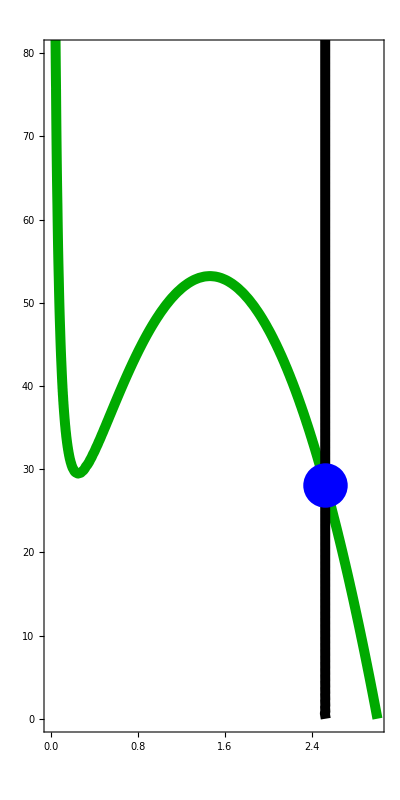

```mathematica
Show[
(*traj,*)
ContourPlot[(dAT3AHp/.{p->Re[solsT3AHp[[7]][[3]][[2]]]})==0,{A,0,10},{H,0,150}, PlotPoints->100, ContourStyle->{Darker[Green],Thickness[0.018]}],
ContourPlot[(dHT3AHp/.{p->Re[solsT3AHp[[7]][[3]][[2]]]})==0,{A,0,10},{H,0,150}, PlotPoints->100, ContourStyle->{Black,Thickness[0.018]}],

Graphics[{PointSize->0.08,Blue,Point[{Re[solsT3AHp[[7]][[1]][[2]]],Re[solsT3AHp[[7]][[2]][[2]]]}]}],

PlotRange->{All,{0,80}},AspectRatio->2,LabelStyle->{Black,16}
]
```

### F3F

```mathematica
Clear[k1,ds]
e = 8;
h = 0.2314;
f = 0.0153;
u = 0.0075;
v = 0.05157;
theta = 0.8;
r = 1;
```

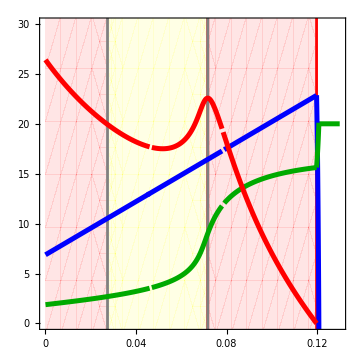

```mathematica
Clear[k1,ds];
k1=2;
P2BT3ASI= Show[
RegionPlot[0.1208> x>0.11977,{x,0,0.13},{y,-1,100}, BoundaryStyle->Blue,PlotStyle->{Blue, Opacity[0.1]}, PlotPoints->100],
RegionPlot[0.11977> x>0.0717,{x,0,0.13},{y,-1,100}, BoundaryStyle->Red,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.02741> x>0.0,{x,0,0.13},{y,-1,100}, BoundaryStyle->None,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.0717> x>0.02741,{x,0,0.13},{y,-1,100}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],

Plot[Re[solsT3ASI[[5]][[3]][[2]]]*10,{ds,0.1208,0.13}, PlotStyle->{Darker[Green],Thickness[0.01]},AspectRatio->1,LabelStyle->16],

Plot[Re[solsT3ASI[[4]][[1]][[2]]],{ds,0.11977,0.1208}, PlotStyle->{Blue,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[solsT3ASI[[4]][[3]][[2]]]*10,{ds,0.11977,0.1208}, PlotStyle->{Darker[Green],Thickness[0.01]},AspectRatio->1,LabelStyle->16],

Plot[Re[solsT3ASI[[7]][[3]][[2]]]*10,{ds,0.079,0.11977}, PlotStyle->{Darker[Green],Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[solsT3ASI[[7]][[1]][[2]]],{ds,0.079,0.11977}, PlotStyle->{Blue,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[solsT3ASI[[7]][[2]][[2]]],{ds,0.0785,0.11977}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

Plot[Re[solsT3ASI[[6]][[3]][[2]]]*10,{ds,0.047,0.078}, PlotStyle->{Darker[Green],Thickness[0.01]},AspectRatio->1,LabelStyle->16,PlotPoints->100],
Plot[Re[solsT3ASI[[6]][[1]][[2]]],{ds,0.045,0.078}, PlotStyle->{Blue,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[solsT3ASI[[6]][[2]][[2]]],{ds,0.047,0.078}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

Plot[Re[solsT3ASI[[8]][[3]][[2]]]*10,{ds,0,0.046}, PlotStyle->{Darker[Green],Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[solsT3ASI[[8]][[1]][[2]]],{ds,0,0.046}, PlotStyle->{Blue,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[solsT3ASI[[8]][[2]][[2]]],{ds,0,0.046}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],


PlotRange->{{0,0.13},{0,30}},
Frame->True,
FrameTicks->{{{0,5,10,15,20,25,30,35},None},{{0,0.02,0.04,0.06,0.08,0.1,0.12},None}},
 LabelStyle->{Black,16},ImageSize->Medium
]
```

### F3H

```mathematica
Clear[e,h,f,dz,u,v,o,theta,r,ds,k1]
```

```mathematica
r*A*(1 - A/k1)-((f*A)/(h^2+A^2))*A*(S+theta*F)
```

```mathematica
FullSimplify[D[r*A*(1 - A/k1)/A,A]]
```

-r/k1

```mathematica
FullSimplify[D[-((f*A)/(h^2+A^2))*A*(S+theta*F)/A,A]]
```

(f (A-h) (A+h) (S+F theta))/((A^2+h^2)^2)

```mathematica
S1=solsT3ASI[[7,1,2]];
F1=solsT3ASI[[7,2,2]];
A1=solsT3ASI[[7,3,2]];
S2=solsT3ASI[[6,1,2]];
F2=solsT3ASI[[6,2,2]];
A2=solsT3ASI[[6,3,2]];
S3=solsT3ASI[[8,1,2]];
F3=solsT3ASI[[8,2,2]];
A3=solsT3ASI[[8,3,2]];
```

```mathematica
SelfLimT3ASI= -r/k1;
C1= (f (A1-h) (A1+h) (S1+F1 theta))/((A1^2+h^2)^2);
C2= (f (A2-h) (A2+h) (S2+F2 theta))/((A2^2+h^2)^2);
C3= (f (A3-h) (A3+h) (S3+F3 theta))/((A3^2+h^2)^2);
C4= (f (solsT3ASI[[4,3,2]]-h) (solsT3ASI[[4,3,2]]+h) (solsT3ASI[[4,1,2]]))/((solsT3ASI[[4,3,2]]^2+h^2)^2);
```

```mathematica
solsT3ASI[[4]]/.{ds->0.05,k1->1}
```

```mathematica
Clear[k1,ds]
e = 8;
h = 0.2314;
f = 0.0153;
u = 0.0075;
v = 0.05157;
theta = 0.8;
r = 1;
```

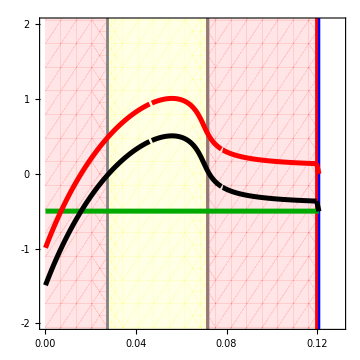

```mathematica
Clear[k1,ds];
k1 = 2;
P3BT3ASI = Show[
RegionPlot[0.1208> x>0.11977,{x,0.12,0.13},{y,-3,3}, BoundaryStyle->Blue,PlotStyle->{Blue, Opacity[0.1]}, PlotPoints->100],
RegionPlot[0.11977> x>0.0717,{x,0,0.13},{y,-3,3}, BoundaryStyle->Red,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.02741> x>0.0,{x,0,0.13},{y,-3,3}, BoundaryStyle->None,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.0717> x>0.02741,{x,0,0.13},{y,-3,3}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],

Plot[Re[SelfLimT3ASI],{ds,0,0.1208}, PlotStyle->{Darker[Green],Thickness[0.01]},AspectRatio->1,LabelStyle->16],

Plot[Re[C1],{ds,0.0717,0.11977}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[C1+SelfLimT3ASI],{ds,0.0717,0.11977}, PlotStyle->{Black,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

Plot[Re[C2],{ds,0.047,0.0777}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[C2+SelfLimT3ASI],{ds,0.047,0.0777}, PlotStyle->{Black,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

Plot[Re[C3],{ds,0,0.046}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[C3+SelfLimT3ASI],{ds,0,0.046}, PlotStyle->{Black,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

Plot[Re[C4],{ds,0.11977,0.1208}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[C4+SelfLimT3ASI],{ds,0.11977,0.1208}, PlotStyle->{Black,Thickness[0.01]},AspectRatio->1,LabelStyle->16],


PlotRange->{{0,0.13},{-2,2}},
Frame->True,
FrameTicks->{{{-2,-1,0,1,2},None},{{{0.00,"0.00"},0.02,0.04, 0.06,0.08,{0.10,"0.10"},0.12},None}}, LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

### Loop Setup

```mathematica
Clear[e,h,f,dz,u,v,o,theta,r,ds,k1]
```

#### Jacobian Elements

```mathematica
J11T3ASI = FullSimplify[D[dAT3ASI,A]];
J12T3ASI = FullSimplify[D[dAT3ASI,S]];
J13T3ASI = FullSimplify[D[dAT3ASI,F]];
J21T3ASI = FullSimplify[D[dST3ASI,A]];
J22T3ASI = FullSimplify[D[dST3ASI,S]];
J23T3ASI = FullSimplify[D[dST3ASI,F]];
J31T3ASI = FullSimplify[D[dFT3ASI,A]];
J32T3ASI = FullSimplify[D[dFT3ASI,S]];
J33T3ASI = FullSimplify[D[dFT3ASI,F]];
```

```mathematica
JMT3ASI= {{J11T3ASI,J12T3ASI,J13T3ASI},{J21T3ASI,J22T3ASI,J23T3ASI},{J31T3ASI,J32T3ASI,J33T3ASI}};
JMT3ASI= JMT3ASI//MatrixForm
```

(r-(2 A r)/k1-(2 A f h^2 (S+F theta))/((A^2+h^2)^2) | -(A^2 f)/(A^2+h^2) | -(A^2 f theta)/(A^2+h^2)
(2 A e f h^2 (S+F theta))/((A^2+h^2)^2) | -ds+(A^2 e f)/(A^2+h^2)-F u | (A^2 e f theta)/(A^2+h^2)-S u
0 | F u | -ds+S u-v)

```mathematica
DJac = {{jAA,jAS,jAF},{jSA,jSS,jSF},{0,jFS,jFF}};
DJac//MatrixForm
```

(jAA | jAS | jAF
jSA | jSS | jSF
0 | jFS | jFF)

```mathematica
CharacteristicPolynomial[DJac,x]
```

CharacteristicPolynomial[DJac,x]

```mathematica
Det[DJac]
```

-jAS jFF jSA+jAF jFS jSA-jAA jFS jSF+jAA jFF jSS

#### Feedbacks & Oscillation Criterion

```mathematica
T3ASIL1 = FullSimplify[(J11T3ASI+J22T3ASI+J33T3ASI)];
T3ASIL2 = FullSimplify[(J12T3ASI*J21T3ASI-J11T3ASI*J22T3ASI)+(-J11T3ASI*J33T3ASI)+(J23T3ASI*J32T3ASI-J22T3ASI*J33T3ASI)];
T3ASIL3= -J12T3ASI J33T3ASI J21T3ASI+J13T3ASI J32T3ASI J21T3ASI-J11T3ASI J32T3ASI J23T3ASI + J11T3ASI J22T3ASI J33T3ASI;
OCT3ASI = (T3ASIL1 T3ASIL2)+T3ASIL3;
```

### Loop Plots (FA3)

```mathematica
Clear[k1,ds]
e = 8;
h = 0.2314;
f = 0.0153;
u = 0.0075;
v = 0.05157;
theta = 0.8;
r = 1;
```

#### FA3A (Upper v. Lower)

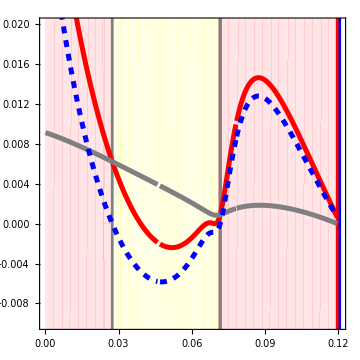

```mathematica
k1=2;
Show[
RegionPlot[0.1208> x>0.11977,{x,0.12,0.13},{y,-3,3}, BoundaryStyle->Blue,PlotStyle->{Blue, Opacity[0.1]}, PlotPoints->100],
RegionPlot[0.11977> x>0.0717,{x,0,0.13},{y,-3,3}, BoundaryStyle->Red,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.02741> x>0.0,{x,0,0.13},{y,-3,3}, BoundaryStyle->None,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.0717> x>0.02741,{x,0,0.13},{y,-3,3}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],

Plot[Re[T3ASIL1* T3ASIL2/.solsT3ASI[[7]]],{ds,0.0785,0.11977}, PlotStyle->{Red,Thickness[0.01]}],
Plot[Re[T3ASIL1* T3ASIL2/.solsT3ASI[[6]]],{ds,0.047,0.0782}, PlotStyle->{Red,Thickness[0.01]}],
Plot[Re[T3ASIL1* T3ASIL2/.solsT3ASI[[8]]],{ds,0,0.046}, PlotStyle->{Red,Thickness[0.01]}],

Plot[Re[-T3ASIL3/.solsT3ASI[[7]]],{ds,0.0785,0.11977}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[-T3ASIL3/.solsT3ASI[[6]]],{ds,0.047,0.0782}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[-T3ASIL3/.solsT3ASI[[8]]],{ds,0,0.046}, PlotStyle->{Gray,Thickness[0.01]}],

Plot[Re[OCT3ASI/.solsT3ASI[[7]]],{ds,0.0785,0.11977}, PlotStyle->{Blue,Dashed,Thickness[0.01]}],
Plot[Re[OCT3ASI/.solsT3ASI[[6]]],{ds,0.047,0.0782}, PlotStyle->{Blue,Dashed,Thickness[0.01]}],
Plot[Re[OCT3ASI/.solsT3ASI[[8]]],{ds,0,0.046}, PlotStyle->{Blue,Dashed,Thickness[0.01]}],

PlotRange->{All,{-0.01,0.02}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

#### FA3B (F1 v. F2)

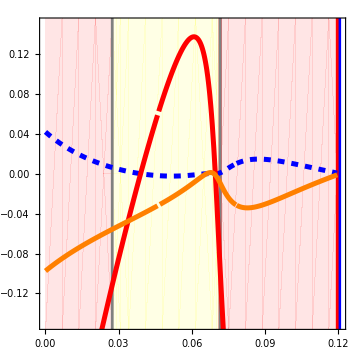

```mathematica
Show[
RegionPlot[0.1208> x>0.11977,{x,0.12,0.13},{y,-3,3}, BoundaryStyle->Blue,PlotStyle->{Blue, Opacity[0.1]}, PlotPoints->100],
RegionPlot[0.11977> x>0.0717,{x,0,0.13},{y,-3,3}, BoundaryStyle->Red,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.02741> x>0.0,{x,0,0.13},{y,-3,3}, BoundaryStyle->None,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.0717> x>0.02741,{x,0,0.13},{y,-3,3}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],

Plot[Re[T3ASIL1* T3ASIL2/.solsT3ASI[[7]]],{ds,0.0785,0.11977}, PlotStyle->{Blue,Dashed,Thickness[0.01]}],
Plot[Re[T3ASIL1* T3ASIL2/.solsT3ASI[[6]]],{ds,0.047,0.0782}, PlotStyle->{Blue,Dashed,Thickness[0.01]}],
Plot[Re[T3ASIL1* T3ASIL2/.solsT3ASI[[8]]],{ds,0,0.046}, PlotStyle->{Blue,Dashed,Thickness[0.01]}],

Plot[Re[T3ASIL1/.solsT3ASI[[7]]],{ds,0.0785,0.11977}, PlotStyle->{Red,Thickness[0.01]}],
Plot[Re[T3ASIL1/.solsT3ASI[[6]]],{ds,0.0465,0.0782}, PlotStyle->{Red,Thickness[0.01]}],
Plot[Re[T3ASIL1/.solsT3ASI[[8]]],{ds,0,0.046}, PlotStyle->{Red,Thickness[0.01]}],

Plot[Re[T3ASIL2/.solsT3ASI[[7]]],{ds,0.0785,0.11977}, PlotStyle->{Orange,Thickness[0.01]}],
Plot[Re[T3ASIL2/.solsT3ASI[[6]]],{ds,0.047,0.0782}, PlotStyle->{Orange,Thickness[0.01]}],
Plot[Re[T3ASIL2/.solsT3ASI[[8]]],{ds,0,0.046}, PlotStyle->{Orange,Thickness[0.01]}],

PlotRange->{All,{-0.15,0.15}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True, PlotRangeClipping->True
]
```

#### FA3C (F1)

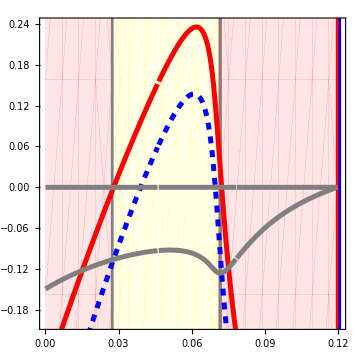

```mathematica
Show[
RegionPlot[0.1208> x>0.11977,{x,0.12,0.13},{y,-3,3}, BoundaryStyle->Blue,PlotStyle->{Blue, Opacity[0.1]}, PlotPoints->100],
RegionPlot[0.11977> x>0.0717,{x,0,0.13},{y,-3,3}, BoundaryStyle->Red,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.02741> x>0.0,{x,0,0.13},{y,-3,3}, BoundaryStyle->None,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.0717> x>0.02741,{x,0,0.13},{y,-3,3}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],

Plot[Re[T3ASIL1/.solsT3ASI[[7]]],{ds,0.0785,0.11977}, PlotStyle->{Blue,Dashed,Thickness[0.01]}],
Plot[Re[T3ASIL1/.solsT3ASI[[6]]],{ds,0.0465,0.0782}, PlotStyle->{Blue,Dashed,Thickness[0.01]}],
Plot[Re[T3ASIL1/.solsT3ASI[[8]]],{ds,0,0.046}, PlotStyle->{Blue,Dashed,Thickness[0.01]}],

Plot[Re[J11T3ASI/.solsT3ASI[[7]]],{ds,0.0785,0.11977}, PlotStyle->{Red,Thickness[0.01]}],
Plot[Re[J11T3ASI/.solsT3ASI[[6]]],{ds,0.0465,0.0782}, PlotStyle->{Red,Thickness[0.01]}],
Plot[Re[J11T3ASI/.solsT3ASI[[8]]],{ds,0,0.046}, PlotStyle->{Red,Thickness[0.01]}],

Plot[Re[J22T3ASI/.solsT3ASI[[7]]],{ds,0.0785,0.11977}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[J22T3ASI/.solsT3ASI[[6]]],{ds,0.0465,0.0782}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[J22T3ASI/.solsT3ASI[[8]]],{ds,0,0.046}, PlotStyle->{Gray,Thickness[0.01]}],

Plot[Re[J33T3ASI/.solsT3ASI[[7]]],{ds,0.0785,0.11977}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[J33T3ASI/.solsT3ASI[[6]]],{ds,0.0465,0.0782}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[J33T3ASI/.solsT3ASI[[8]]],{ds,0,0.046}, PlotStyle->{Gray,Thickness[0.01]}],

PlotRange->{All,{-0.2,0.24}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

#### FA3D (F2)

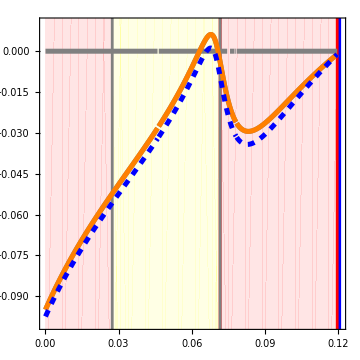

```mathematica
Show[
RegionPlot[0.1208> x>0.11977,{x,0.12,0.13},{y,-3,3}, BoundaryStyle->Blue,PlotStyle->{Blue, Opacity[0.1]}, PlotPoints->100],
RegionPlot[0.11977> x>0.0717,{x,0,0.13},{y,-3,3}, BoundaryStyle->Red,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.02741> x>0.0,{x,0,0.13},{y,-3,3}, BoundaryStyle->None,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.0717> x>0.02741,{x,0,0.13},{y,-3,3}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],

Plot[Re[(J12T3ASI*J21T3ASI-J11T3ASI*J22T3ASI)/.solsT3ASI[[7]]],{ds,0.0785,0.11977}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[(J12T3ASI*J21T3ASI-J11T3ASI*J22T3ASI)/.solsT3ASI[[6]]],{ds,0.0465,0.0782}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[(J12T3ASI*J21T3ASI-J11T3ASI*J22T3ASI)/.solsT3ASI[[8]]],{ds,0,0.046}, PlotStyle->{Gray,Thickness[0.01]}],

Plot[Re[(-J11T3ASI*J33T3ASI)/.solsT3ASI[[7]]],{ds,0.0785,0.11977}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[(-J11T3ASI*J33T3ASI)/.solsT3ASI[[6]]],{ds,0.0465,0.0782}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[(-J11T3ASI*J33T3ASI)/.solsT3ASI[[8]]],{ds,0,0.046}, PlotStyle->{Gray,Thickness[0.01]}],

Plot[Re[(J12T3ASI*J21T3ASI-J11T3ASI*J22T3ASI)/.solsT3ASI[[7]]],{ds,0.0785,0.11977}, PlotStyle->{Orange,Thickness[0.01]}],
Plot[Re[(J12T3ASI*J21T3ASI-J11T3ASI*J22T3ASI)/.solsT3ASI[[6]]],{ds,0.0465,0.0782}, PlotStyle->{Orange,Thickness[0.01]}],
Plot[Re[(J12T3ASI*J21T3ASI-J11T3ASI*J22T3ASI)/.solsT3ASI[[8]]],{ds,0,0.046}, PlotStyle->{Orange,Thickness[0.01]}],

Plot[Re[T3ASIL2/.solsT3ASI[[7]]],{ds,0.0785,0.11977}, PlotStyle->{Blue,Dashed,Thickness[0.01]}],
Plot[Re[T3ASIL2/.solsT3ASI[[6]]],{ds,0.0465,0.0782}, PlotStyle->{Blue,Dashed,Thickness[0.01]}],
Plot[Re[T3ASIL2/.solsT3ASI[[8]]],{ds,0,0.046}, PlotStyle->{Blue,Dashed,Thickness[0.01]}],

PlotRange->{All,{-0.1,0.01}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True, PlotRangeClipping->True
]
```

#### FA3E

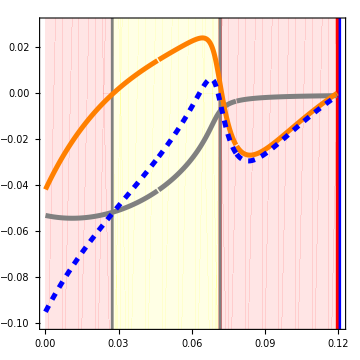

```mathematica
Show[
RegionPlot[0.1208> x>0.11977,{x,0.12,0.13},{y,-3,3}, BoundaryStyle->Blue,PlotStyle->{Blue, Opacity[0.1]}, PlotPoints->100],
RegionPlot[0.11977> x>0.0717,{x,0,0.13},{y,-3,3}, BoundaryStyle->Red,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.02741> x>0.0,{x,0,0.13},{y,-3,3}, BoundaryStyle->None,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.0717> x>0.02741,{x,0,0.13},{y,-3,3}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],

Plot[Re[(J12T3ASI*J21T3ASI)/.solsT3ASI[[7]]],{ds,0.0785,0.11977}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[(J12T3ASI*J21T3ASI)/.solsT3ASI[[6]]],{ds,0.0465,0.0782}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[(J12T3ASI*J21T3ASI)/.solsT3ASI[[8]]],{ds,0,0.046}, PlotStyle->{Gray,Thickness[0.01]}],

Plot[Re[(-J11T3ASI*J22T3ASI)/.solsT3ASI[[7]]],{ds,0.0785,0.11977}, PlotStyle->{Orange,Thickness[0.01]}],
Plot[Re[(-J11T3ASI*J22T3ASI)/.solsT3ASI[[6]]],{ds,0.0465,0.0782}, PlotStyle->{Orange,Thickness[0.01]}],
Plot[Re[(-J11T3ASI*J22T3ASI)/.solsT3ASI[[8]]],{ds,0,0.046}, PlotStyle->{Orange,Thickness[0.01]}],

Plot[Re[(J12T3ASI*J21T3ASI-J11T3ASI*J22T3ASI)/.solsT3ASI[[7]]],{ds,0.0785,0.11977}, PlotStyle->{Blue, Dashed,Thickness[0.01]}],
Plot[Re[(J12T3ASI*J21T3ASI-J11T3ASI*J22T3ASI)/.solsT3ASI[[6]]],{ds,0.0465,0.0782}, PlotStyle->{Blue, Dashed,Thickness[0.01]}],
Plot[Re[(J12T3ASI*J21T3ASI-J11T3ASI*J22T3ASI)/.solsT3ASI[[8]]],{ds,0,0.046}, PlotStyle->{Blue, Dashed,Thickness[0.01]}],

PlotRange->{All,{-0.1,0.03}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True, PlotRangeClipping->True
]
```

### Exotica (FA6)

#### FA6B

```mathematica
Clear[k1,ds]
e = 8;
h = 0.2314;
f = 0.0153;
u = 0.0075;
v = 0.05157;
theta = 0.8;
r = 1;
ds = 0.01732;
TS1=ParametricNDSolveValue[{A'[t]== r*A[t]*(1 - A[t]/k1)-((f*A[t])/(h^2+A[t]^2))*A[t]*(S[t]+theta*F[t]),
S'[t]==e*((f*A[t])/(h^2+A[t]^2))*A[t]*(S[t]+theta*F[t]) - ds*S[t] - u*S[t]*F[t],
F'[t]==u*S[t]*F[t] - (ds + v)*F[t],
A[0]==0.242686473,
S[0]==14.74,
F[0]==17.13171749359,
WhenEvent[t==1000,A[t]->0.5]},{A,S,F},{t,0,6000},{k1}];
Manipulate[
Show[LogPlot[Evaluate[#[t]& /@TS1[k1]],{t,0,5500},PlotRange->{{950,1150},{0.05,100}}, PlotStyle->{{Darker[Green],Thick},{Blue,Thick}, {Red,Thick}},TicksStyle->10,AspectRatio->1, LabelStyle->16, Frame->True, (*FrameTicks->{{{{0.1,"0.1"},{1.0,"1.0"},{10.0,"10.0"},{100.0,"100.0"}},None},{{{600,"0"},{700,"100"},{800,"200"}},None}}, *)
FrameStyle->Black],
Graphics[{Directive[Dashed,Thick, Darker[Gray]],InfiniteLine[{{1000,0},{1000,5}}]}]],
{{k1,4},1,8}]
```

#### FA6C (Nullclines)

```mathematica
Clear[e,h,f,dh,u,v,theta,r,k1,p]
```

```mathematica
T3AHp = DynamicalSystem[{
r*A*(1 - A/k1)-H*f((1-p)+theta p)(A^2/(h^2+A^2)),
e*f((1-p)+theta p)(A^2/(h^2+A^2))*H - (dh+p v)*H  ,
p ((u H-v) (1-p)-e f((1-p)+theta p)(A^2/(h^2+A^2)))
},
{{A,-0.01,10},{H,-0.01,200}, {p,0,1}},
{{e,0,1000},{h,0,1},{f,0,1},{dh,0.001,0.14},{u,0,2},{v,0,0.2},{theta,0,1},{r,0,2},{k1,0.01,6}}];
```

```mathematica
T3AHp = T3AHp/.{e->8,h -> 0.2314, f->0.0153, u->0.0075, v->0.05157, theta->1, r->1}
```

DynamicalSystem[«3 ODEs»,{A,H,p},{dh,k1},{e→8,f→0.0153,h→0.2314,r→1,theta→1,u→0.0075,v→0.05157}]

```mathematica
traj = DisplayTrajectories[T3AHp/.{k1->5,dh->0.0808},{{0.68102,19.81343,0.6830988}},800, StateVariables->{A,H}, MaxSteps->Infinity, PlotRange->{{0,All},{0,All}}, PlotStyle->{Blue,Thickness[0.008]},FrameLabel->None];
```

```mathematica
Last[First[$Trajectories]]
```

{0.681029,19.8134,0.683099}

```mathematica
dAT3AHp = r*A*(1 - A/k1)-H*f((1-p)+theta p)(A^2/(h^2+A^2));
dHT3AHp = e*f((1-p)+theta p)(A^2/(h^2+A^2))*H - (dh+p v)*H ;
dpT3AHp=p ((u H-v) (1-p)-e f((1-p)+theta p)(A^2/(h^2+A^2)));
```

```mathematica
Clear[dh];
e = 8;
h = 0.2314;
f = 0.0153;
u = 0.0075;
v = 0.05157;
theta = 1;
r = 1;
k1=5;
dh = 0.0807;
```

```mathematica
solsT3AHp = Solve[{dAT3AHp==0 ,dHT3AHp==0,dpT3AHp==0},{A,H,p}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
solsT3AHp
```

{{A→-0.321908,H→-33.9661,p→0.},{A→0.,H→0.,p→1.},{A→0.,H→6.876,p→-1.56486},{A→0.321908,H→29.8571,p→0.},{A→0.839382,H→49.1211,p→0.640969},{A→1.8496,H→77.3619,p→0.772033},{A→2.31101,H→82.0469,p→0.78505},{A→5.,H→0.,p→0.},{A→5.,H→0.,p→3.3684},{A→0.,H→0.,p→0.}}

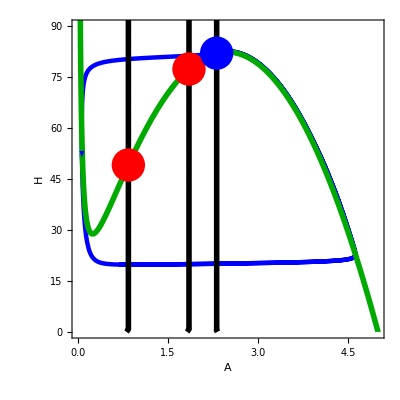

```mathematica
Show[
traj,
ContourPlot[(dAT3AHp/.{p->solsT3AHp[[5]][[3]][[2]]})==0,{A,0,10},{H,0,150}, PlotPoints->100, ContourStyle->{Darker[Green],Thickness[0.01]}],

ContourPlot[(dHT3AHp/.{p->solsT3AHp[[5]][[3]][[2]]})==0,{A,0,10},{H,0,150}, PlotPoints->100, ContourStyle->{Black,Thickness[0.01]}],

ContourPlot[(dHT3AHp/.{p->solsT3AHp[[6]][[3]][[2]]})==0,{A,0,10},{H,0,150}, PlotPoints->100, ContourStyle->{Black,Thickness[0.01]}],

ContourPlot[(dHT3AHp/.{p->solsT3AHp[[7]][[3]][[2]]})==0,{A,0,10},{H,0,150}, PlotPoints->100, ContourStyle->{Black,Thickness[0.01]}],


Graphics[{PointSize->0.06,Red,Point[{solsT3AHp[[5]][[1]][[2]],solsT3AHp[[5]][[2]][[2]]}]}],
Graphics[{PointSize->0.06,Red,Point[{solsT3AHp[[6]][[1]][[2]],solsT3AHp[[6]][[2]][[2]]}]}],
Graphics[{PointSize->0.06,Blue,Point[{solsT3AHp[[7]][[1]][[2]],solsT3AHp[[7]][[2]][[2]]}]}],

PlotRange->{All,{0,90}},LabelStyle->{Black,16}
]
```

#### FA6D

```mathematica
Clear[k1,ds]
e = 8;
h = 0.2314;
f = 0.0153;
u = 0.0075;
v = 0.05157;
theta = 1;
r = 1;
ds = 0.0809;
TS2=ParametricNDSolveValue[{A'[t]== r*A[t]*(1 - A[t]/k1)-((f*A[t])/(h^2+A[t]^2))*A[t]*(S[t]+theta*F[t]),
S'[t]==e*((f*A[t])/(h^2+A[t]^2))*A[t]*(S[t]+theta*F[t]) - ds*S[t] - u*S[t]*F[t],
F'[t]==u*S[t]*F[t] - (ds + v)*F[t],
A[0]==0.05,
S[0]==5,
F[0]==5},{A,S,F},{t,0,6000},{k1}];
Manipulate[
Show[LogPlot[Evaluate[#[t]& /@TS2[k1]],{t,0,5500},PlotRange->{{0,700},{0.02,200}}, PlotStyle->{{Darker[Green],Thick},{Blue,Thick}, {Red,Thick}},TicksStyle->10,AspectRatio->1/2.5, LabelStyle->16, Frame->True, (*FrameTicks->{{{{0.1,"0.1"},{1.0,"1.0"},{10.0,"10.0"},{100.0,"100.0"}},None},{{{600,"0"},{700,"100"},{800,"200"}},None}}, *)
FrameStyle->Black]],
{{k1,5},1,8}]
```